This notebook implements all comparative analyses. First, it generates transformed generating functions using time parameters in years rather than coalescent units. It then implements the cluster tests for potentially co - diverged species and finally the mixtures distributions. 
Initialise 1 _fileS1 and then initialise this notebook and evaluate the CalibratingModels section of 4_ModelFitting_Calibration

## Transformed GFs - full and simplified

```mathematica
bestSpecies
```

{Onit,Cfun,Taur,Mdor,Msti,Ebru,Eann,Sumb,Opom,Bpal,Neusal,Andgro,Neuqba}

#### Cfun (16 -T1Z)

```mathematica
solX2X3IaXZ=Get["/Users/ingrid/Dropbox/MATHEMATICA/BunnefeldEtAl_Scripts/solX2X3IaXZ.m"];
```

```mathematica
solX2X3IaXZA=Apart[#]&/@(solX2X3IaXZ);
```

```mathematica
cfunBestModF=GFtransform[solX2X3IaXZA,271,3.5*10^-9,0.5];
```

```mathematica
solX2X3IaXZAT1Z=Apart[#]&/@(solX2X3IaXZ/.T1->0);
```

```mathematica
cfunBestModS=GFtransformT1Z[solX2X3IaXZAT1Z,271,3.5*10^-9,0.5];
```

#### Mdor (6 -TAZ)

```mathematica
solY2Z3IaYZ=Get["/Users/ingrid/Dropbox/MATHEMATICA/BunnefeldEtAl_Scripts/solY2Z3IaYZ.m"];
```

```mathematica
solY2Z3IaYZA=Apart[#]&/@(solY2Z3IaYZ);
```

```mathematica
mdorBestModF=GFtransform[solY2Z3IaYZA,743,3.5*10^-9,0.5];
```

```mathematica
solY2Z3IaYZATAZ=Apart[#]&/@(solY2Z3IaYZ/.A1->0);
```

```mathematica
mdorBestModS=GFtransformTAZ[solY2Z3IaYZATAZ,743,3.5*10^-9,0.5];
```

#### Taur (12 -POLY)

```mathematica
solX2Z3IaXZ=Get["/Users/ingrid/Dropbox/MATHEMATICA/BunnefeldEtAl_Scripts/solX2Z3IaXZ.m"];
```

```mathematica
solX2Z3IaXZA=Apart[#]&/@(solX2Z3IaXZ);
```

```mathematica
taurBestModF=GFtransform[solX2Z3IaXZA,247,3.5*10^-9,0.5];
```

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

```mathematica
solX2Z3IaXZApoly=Apart[#]&/@(solX2Z3IaXZ/.{T2->0,a1->0,A1->0});
```

```mathematica
taurBestModS=GFtransformPOLY[solX2Z3IaXZApoly,247,3.5*10^-9,0.5];
```

#### Msti (7 -POLY)

```mathematica
solY2Z3IaZX=Get["/Users/ingrid/Dropbox/MATHEMATICA/BunnefeldEtAl_Scripts/solY2Z3IaZX.m"];
```

```mathematica
solY2Z3IaZXA=Apart[#]&/@(solY2Z3IaZX);
```

```mathematica
mstiBestModF=GFtransform[solY2Z3IaZXA,1455,3.5*10^-9,1]
```

```mathematica
solY2Z3IaZXApoly=Apart[#]&/@(solY2Z3IaZX/.{T2->0,a1->0,A1->0});
```

```mathematica
mstiBestModS=GFtransformPOLY[solY2Z3IaZXApoly,1455,3.5*10^-9,1];
```

#### Ebru (4 -TAZ)

```mathematica
solY2Y3IaXZ=Get["/Users/ingrid/Dropbox/MATHEMATICA/BunnefeldEtAl_Scripts/solY2Y3IaXZ.m"];
```

```mathematica
solY2Y3IaXZA=Apart[#]&/@(solY2Y3IaXZ);
```

```mathematica
ebruBestModF=GFtransform[solY2Y3IaXZA,178,3.5*10^-9,0.5];
```

```mathematica
solY2Y3IaXZATAZ=Apart[#]&/@(solY2Y3IaXZ/.A1->0);
```

```mathematica
ebruBestModS=GFtransformTAZ[solY2Y3IaXZATAZ,178,3.5*10^-9,0.5];
```

#### Onit (1 - NOADM)

```mathematica
solY2Y3IaZY=Get["/Users/ingrid/Dropbox/MATHEMATICA/BunnefeldEtAl_Scripts/solY2Y3IaZY.m"];
```

```mathematica
solY2Y3IaZYA=Apart[#]&/@(solY2Y3IaZY)
```

```mathematica
onitBestModF=GFtransform[solY2Y3IaZYA,442,3.5*10^-9,0.5];
```

```mathematica
solY2Y3IaZYANoadm=Apart[#]&/@(solY2Y3IaZY/.{A1->0,a1->0});
```

```mathematica
onitBestModS=GFtransformNOADM[solY2Y3IaZYANoadm,442,3.5*10^-9,0.5];
```

#### Eann (9 - NOADM)

```mathematica
solX2Z3IaZY=Get["/Users/ingrid/Dropbox/MATHEMATICA/BunnefeldEtAl_Scripts/solX2Z3IaZY.m"];
```

```mathematica
solX2Z3IaZYA=Apart[#]&/@(solX2Z3IaZU);
```

```mathematica
eannBestModF=GFtransform[solX2Z3IaZYA,438,3.5*10^-9,0.5];
```

```mathematica
solX2Z3IaZYa=Apart[#]&/@(solX2Z3IaZY/.{A1->0,a1->0})//Simplify
```

```mathematica
eannBestModS=GFtransformNOADM[solX2Z3IaZYa,438,3.5*10^-9,0.5];
```

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

```mathematica
Export["/home/lb57/Dropbox/Edinburgh_InUse/Genomics Lab/ReAnalysisSpring2017/eannNOADMFB.m",eannBestModS]
```

#### Opom (13 - NO ADM)

```mathematica
solX2X3IaZY=Get["/Users/ingrid/Dropbox/MATHEMATICA/BunnefeldEtAl_Scripts/solX2X3IaZY.m"];
```

```mathematica
solX2X3IaZYA=Apart[#]&/@(solX2X3IaZY);
```

```mathematica
opomBestModF=GFtransform[solX2X3IaZYA,253,3.5*10^-9,0.5];
```

```mathematica
solX2X3IaZYa=Apart[#]&/@(solX2X3IaZY/.{A1->0,a1->0})//Simplify;
```

```mathematica
opomBestModS=GFtransformNOADM[solX2X3IaZYa,253,3.5*10^-9,0.5];
```

```mathematica
Export["/home/lb57/Dropbox/Edinburgh_InUse/Genomics Lab/ReAnalysisSpring2017/opomNOADMFB.m",opomBestModS]
```

/home/lb57/Dropbox/Edinburgh_InUse/Genomics Lab/ReAnalysisSpring2017/opomNOADMFB.m

#### Sumb - (6 - T1Z)

```mathematica
solY2Z3IaYZ=Get["/Users/ingrid/Dropbox/MATHEMATICA/BunnefeldEtAl_Scripts/solY2Z3IaYZ.m"];
```

```mathematica
solY2Z3IaYZA=Apart[#]&/@(solY2Z3IaYZ);
```

```mathematica
sumbBestModF=GFtransform[solY2Z3IaYZA,411,3.5*10^-9,0.5];
```

```mathematica
solY2Z3IaYZAT1Z=Apart[#]&/@(solY2Z3IaYZ/.T1->0);
```

```mathematica
sumbBestModS=GFtransformT1Z[solY2Z3IaYZAT1Z,411,3.5*10^-9,0.5];
```

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

#### Bpal - (11 - TAZ)

```mathematica
solX2Z3IaZX=Get["/Users/ingrid/Dropbox/MATHEMATICA/BunnefeldEtAl_Scripts/solX2Z3IaZX.m"];
```

```mathematica
solX2Z3IaZXA=Apart[#]&/@(solX2Z3IaZX);
```

```mathematica
bpalBestModF=GFtransform[solX2Z3IaZXA,563,3.5*10^-9,0.5];
```

```mathematica
solX2Z3IaZXa=Apart[#]&/@(solX2Z3IaZX/.{A1->0,a1->0})//Simplify
```

```mathematica
bpalBestModS=GFtransformNOADM[solX2Z3IaZXa,563,3.5*10^-9,0.5];
```

```mathematica
solX2Z3IaZXATAZ=Apart[#]&/@(solX2Z3IaZX/.A1->0);
```

```mathematica
bpalBestModS=GFtransformTAZ[solX2Z3IaZXATAZ,563,3.5*10^-9,0.5];
```

#### Andgro (7 - full)

```mathematica
solY2Z3IaZX=Get["/Users/ingrid/Dropbox/MATHEMATICA/BunnefeldEtAl_Scripts/solY2Z3IaZX.m"];
```

```mathematica
solY2Z3IaZXa=Apart[#]&/@(solY2Z3IaZX);
```

```mathematica
andgroBestModF=GFtransform[solY2Z3IaZXa,652,3.5*10^-9,0.5];
```

```mathematica
solY2Z3IaZXa=Apart[#]&/@(solY2Z3IaZX/.{A1->0,a1->0})//Simplify
```

```mathematica
andgroBestModS=GFtransformNOADM[solY2Z3IaZXa,652,3.5*10^-9,0.5];
```

#### Neuqba - (6 - T1Z)

```mathematica
solY2Z3IaYZ=Get["/Users/ingrid/Dropbox/MATHEMATICA/BunnefeldEtAl_Scripts/solY2Z3IaYZ.m"];
```

```mathematica
solY2Z3IaYZa=Apart[#]&/@solY2Z3IaYZ
```

```mathematica
neuqbaBestModF=GFtransform[solY2Z3IaYZa,182,3.5*10^-9,0.5];
```

```mathematica
solY2Z3IaYZAT1Z=Apart[#]&/@(solY2Z3IaYZ/.T1->0);
```

```mathematica
neuqbaBestModS=GFtransformT1Z[solY2Z3IaYZAT1Z,182,3.5*10^-9,0.5];
```

#### Neusal (3 - NOADM)

```mathematica
solY2Y3IaZX=Get["/Users/ingrid/Dropbox/MATHEMATICA/BunnefeldEtAl_Scripts/solY2Y3IaZX.m"];
```

```mathematica
solY2Y3IaZXa=Apart[#]&/@solY2Y3IaZX;
```

```mathematica
neusalBestModF=GFtransform[solY2Y3IaZXa,250,3.5*10^-9,0.5];
```

```mathematica
solY2Y3IaZXAT1Z=Apart[#]&/@(solY2Y3IaZX/.T1->0);
```

```mathematica
neusalBestModS=GFtransformT1Z[solY2Y3IaZXAT1Z,250,3.5*10^-9,0.5];
```

```mathematica
solY2Y3IaZXa=Apart[#]&/@(solY2Y3IaZX/.{A1->0,a1->0})//Simplify;
```

```mathematica
neusalBestModS=GFtransformNOADM[solY2Y3IaZXa,250,3.5*10^-9,0.5];
```

#### Collating model transforms

```mathematica
fullTransMods={onitBestModF,cfunBestModF,taurBestModF,mdorBestModF,mstiBestModF,ebruBestModF,eannBestModF,sumbBestModF,opomBestModF,bpalBestModF,neusalBestModF,andgroBestModF,neuqbaBestModF};
```

```mathematica
Export["/home/lb57/Dropbox/MATHEMATICA/BunnefeldEtAl_Scripts/GFs/bestModFull_FB_Mar17.m",fullTransMods]
```

/home/lb57/Dropbox/Edinburgh_InUse/Genomics Lab/ReAnalysisSpring2017/bestModFull_FB_Mar17.m

```mathematica
TransMods={onitBestModS,cfunBestModS,taurBestModS,mdorBestModS,mstiBestModS,ebruBestModS,eannBestModS,sumbBestModS,opomBestModS,bpalBestModS,neusalBestModS,andgroBestModS,neuqbaBestModS};
```

```mathematica
Export["/home/lb57/Dropbox/MATHEMATICA/BunnefeldEtAl_Scripts/GFs/bestModSimp_FB_Mar17.m",TransMods]
```

```mathematica
fullTransMods=Get["/home/lb57/Dropbox/MATHEMATICA/BunnefeldEtAl_Scripts/GFs/bestModFull_FB_Mar17.m"];
```

```mathematica
TransMods=Get["/home/lb57/Dropbox/MATHEMATICA/BunnefeldEtAl_Scripts/GFs/bestModSimp_FB_Mar17.m"];
```

## Testing for co-divergence clusters

```mathematica
bestSpecies={"Onit","Cfun","Taur","Mdor","Msti","Ebru","Eann","Sumb","Opom","Bpal","Neusal","Andgro","Neuqba"}
```

{Onit,Cfun,Taur,Mdor,Msti,Ebru,Eann,Sumb,Opom,Bpal,Neusal,Andgro,Neuqba}

Clusters to test:  Eann, Bpal;Taur, Mdor; Neuqba, Ebru

Eann, Bpal

```mathematica
EB={t2BestScaled[[7]],t2BestScaled[[10]]}
```

{130854.,135086.}

```mathematica
EBgrid={Min[EB],Max[EB],(Max[EB]-Min[EB])/20}
```

{130854.,135086.,211.597}

```mathematica
EBgridf=Table[i,{i,Min[EB],Max[EB],(Max[EB]-Min[EB])/20}]
```

{130854.,131065.,131277.,131488.,131700.,131912.,132123.,132335.,132546.,132758.,132970.,133181.,133393.,133604.,133816.,134028.,134239.,134451.,134662.,134874.,135086.}

Taur, Mdor

```mathematica
TM={t2BestScaled[[3]],t2BestScaled[[4]]}
```

{79768.7,89702.7}

```mathematica
TMgrid={Min[TM],Max[TM],(Max[TM]-Min[TM])/20}
```

{79768.7,89702.7,496.701}

```mathematica
TMgridf=Table[i,{i,Min[TM],Max[TM],(Max[TM]-Min[TM])/20}]
```

{79768.7,80265.4,80762.1,81258.8,81755.5,82252.2,82748.9,83245.6,83742.3,84239.,84735.7,85232.4,85729.1,86225.8,86722.5,87219.2,87715.9,88212.6,88709.3,89206.,89702.7}

Neuqba, Ebru

```mathematica
EN={t2BestScaled[[6]],t2BestScaled[[13]]}
```

{1.05154×10^6,1.17475×10^6}

```mathematica
ENgrid={Min[EN],Max[EN],(Max[EN]-Min[EN])/20}
```

{1.05154×10^6,1.17475×10^6,6160.69}

```mathematica
ENgridf=Table[i,{i,Min[EN],Max[EN],(Max[EN]-Min[EN])/20}]
```

{1.05154×10^6,1.0577×10^6,1.06386×10^6,1.07002×10^6,1.07618×10^6,1.08234×10^6,1.0885×10^6,1.09466×10^6,1.10082×10^6,1.10699×10^6,1.11315×10^6,1.11931×10^6,1.12547×10^6,1.13163×10^6,1.13779×10^6,1.14395×10^6,1.15011×10^6,1.15627×10^6,1.16243×10^6,1.16859×10^6,1.17475×10^6}

```mathematica
TransMods=Get["/home/lb57/Dropbox/MATHEMATICA/BunnefeldEtAl_Scripts/GFs/bestModSimp_FB_Mar17.m"];
```

```mathematica
maxCurve[tTest_, blocks_] := (#[[1]] & /@ tTest - Max[(#[[1]] & /@ tTest)])*blocks
```

#### Eann (briefly annotated)

Read in data

```mathematica
EannconfigFB=ReadList["/Users/ingrid/Dropbox/MATHEMATICA/BunnefeldEtAl_Scripts/SpeciesMutationalConfigs/EannconfigFB.txt"]
```

{SparseArray[<16>, {4, 4}],SparseArray[<16>, {4, 4}],SparseArray[<16>, {4, 4}],SparseArray[<16>, {4, 4}],SparseArray[<16>, {4, 4}],SparseArray[<16>, {4, 4}],SparseArray[<64>, {4, 4, 4}]}

Read in solved GF

```mathematica
eannBestModS=TransMods[[7]];
```

Block number

```mathematica
eannCount=Total[Normal[EannconfigFB[[1]]//Normal//Flatten]]
```

269892

```mathematica
AbsoluteTiming[testeannT2=ModelNOADTabT2x[eannBestModS,EannconfigFB,{0.5,1.5},{25000,55000},EBgrid,{0.1,1},{0.1,1},2,150]]
```

{5564.57,{{-5.06785×10^6,{theta→0.947958,t1→40540.1,xx→0.372781,yy→0.157166}},{-5.06786×10^6,{theta→0.947017,t1→40494.7,xx→0.372257,yy→0.156833}},{-5.06787×10^6,{theta→0.946107,t1→40474.4,xx→0.372002,yy→0.156985}},{-5.06788×10^6,{theta→0.945116,t1→40486.7,xx→0.371685,yy→0.156932}},{-5.0679×10^6,{theta→0.944373,t1→40475.1,xx→0.371465,yy→0.156468}},{-5.06791×10^6,{theta→0.943328,t1→40389.7,xx→0.370909,yy→0.156617}},{-5.06793×10^6,{theta→0.942306,t1→40347.7,xx→0.370375,yy→0.156786}},{-5.06795×10^6,{theta→0.941485,t1→40333.3,xx→0.370154,yy→0.155698}},{-5.06796×10^6,{theta→0.940579,t1→40296.5,xx→0.369797,yy→0.156412}},{-5.06798×10^6,{theta→0.939639,t1→40299.2,xx→0.369507,yy→0.156276}},{-5.068×10^6,{theta→0.938727,t1→40227.2,xx→0.369068,yy→0.156003}},{-5.06802×10^6,{theta→0.937795,t1→40208.4,xx→0.368664,yy→0.155972}},{-5.06804×10^6,{theta→0.936897,t1→40189.2,xx→0.36835,yy→0.155898}},{-5.06806×10^6,{theta→0.935961,t1→40142.3,xx→0.367983,yy→0.155922}},{-5.06809×10^6,{theta→0.935064,t1→40125.5,xx→0.367599,yy→0.155691}},{-5.06811×10^6,{theta→0.934144,t1→40093.,xx→0.367246,yy→0.155548}},{-5.06859×10^6,{theta→0.934146,t1→25000.,xx→0.330009,yy→0.151856}},{-5.06861×10^6,{theta→0.933217,t1→25000.,xx→0.329773,yy→0.151845}},{-5.06818×10^6,{theta→0.931395,t1→40012.5,xx→0.366161,yy→0.155253}},{-5.06821×10^6,{theta→0.930457,t1→39996.,xx→0.365785,yy→0.155033}},{-5.06823×10^6,{theta→0.929537,t1→39954.8,xx→0.365383,yy→0.15493}}}}

Replot curve assume 2000 independent blocks

```mathematica
eannMax2=maxCurve[testeannT2/eannCount,2000]
```

{0.,-0.0893013,-0.184348,-0.285275,-0.392075,-0.504451,-0.62281,-0.746995,-0.876794,-1.01251,-1.15401,-1.3013,-1.45438,-1.61327,-1.77791,-1.94835,-5.52842,-5.69661,-2.49434,-2.68789,-2.88721}

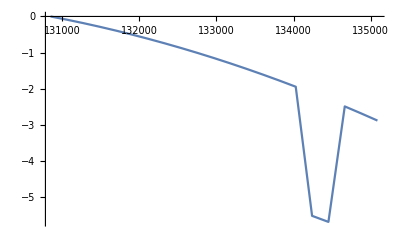

```mathematica
ListPlot[{EBgridf,eannMax2}//Thread,Joined->True]
```

(Can proceed even though two points on the curve not well - estimated)

#### Bpal

```mathematica
BpalconfigFB=ReadList["/Users/ingrid/Dropbox/MATHEMATICA/BunnefeldEtAl_Scripts/SpeciesMutationalConfigs/BpalconfigFB.txt"];
```

```mathematica
bpalCount=Total[Normal[BpalconfigFB[[2]]//Normal//Flatten]]
```

265858

```mathematica
bpalBestModS=TransMods[[10]];
```

```mathematica
ModelTAZTabT2x5[model_,configs_,{θL_,θU_},{tt1L_,tt1U_},{tt2L_,tt2U_,s_},{xxL_,xxU_},{yyL_,yyU_},{a1L_,a1U_},max_,iter_,qq_,rr_]:=ParallelTable[NMaximize[{Total[Table[totallnL[{model[[i]]},ω,theta,{λ[{x}]->xx,λ[{y}]->yy,tt1->t1,a1->aa1},max,configs[[i]]],{i,qq,7}]],yyU>yy>yyL,xxU>xx>xxL,tt1U>t1>tt1L,θU>theta>θL,a1U>aa1>a1L},{theta,t1,xx,yy,aa1},MaxIterations->iter,Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False,RandomSeed->4}],{realT2,tt2L,tt2U,s}];
```

```mathematica
AbsoluteTiming[testbpalT2new=ModelTAZTabT2x5[bpalBestModS,BpalconfigFB,{0.5,1.5},{10000,40000},EBgrid,{0.1,2},{2,10},{0,0.15},2,150,3,7]]
```

```mathematica
testbpalT2new={{-3.6363918794524516*^6,{theta->1.045097959206363,t1->15563.652341681256,xx->0.1918384480723377,yy->8.07588612810779,aa1->0.11071963122749043}},{-3.636371328410279*^6,{theta->1.0441329788832878,t1->15436.25675537901,xx->0.19316945143033873,yy->8.189627623945011,aa1->0.11211878247979967}},{-3.636357198970491*^6,{theta->1.0444568637178486,t1->15331.872492232113,xx->0.19459236692758453,yy->8.235503269620516,aa1->0.11357100671074054}},{-3.63634462081957*^6,{theta->1.0428424419781561,t1->15484.489563941273,xx->0.19567275070712772,yy->8.14706429498781,aa1->0.11451427525217193}},{-3.6363319591848934*^6,{theta->1.0421282481861218,t1->15331.154550202149,xx->0.1950363397830569,yy->8.21769419301432,aa1->0.11464676223150319}},{-3.6363202776297387*^6,{theta->1.041235434945019,t1->15333.850494692528,xx->0.19538495686086277,yy->8.20581914245101,aa1->0.11514168176886136}},{-3.63631012819735*^6,{theta->1.0389096222665708,t1->15392.263245285236,xx->0.1937522725400314,yy->8.153926104441371,aa1->0.11452937082648516}},{-3.636299521997438*^6,{theta->1.0390427092902825,t1->14980.084852148675,xx->0.19508738609047677,yy->8.364907249554841,aa1->0.11584966994281304}},{-3.636289316613923*^6,{theta->1.0383794641659163,t1->15310.258577141774,xx->0.19616679084416533,yy->8.17888840719949,aa1->0.11684627458434231}},{-3.636296548806973*^6,{theta->1.0350225450914055,t1->16491.215692599064,xx->0.19524486553153197,yy->7.5902681475224885,aa1->0.11874393451540355}},{-3.636271287438912*^6,{theta->1.0359482217887628,t1->15301.33407389353,xx->0.1963409982927112,yy->8.17663887505114,aa1->0.11752285286045572}},{-3.6362635776130958*^6,{theta->1.034900168662955,t1->15313.639361987523,xx->0.19702388472362212,yy->8.14826021573126,aa1->0.1180081858952855}},{-3.636276981041519*^6,{theta->1.0353142531808532,t1->16826.240552003717,xx->0.19855275445766607,yy->7.460603437511254,aa1->0.12125720615792646}},{-3.6362525888621267*^6,{theta->1.0346658765758487,t1->15780.379124513956,xx->0.19964303846477094,yy->7.944377242976432,aa1->0.1175638096912209}},{-3.636246647678554*^6,{theta->1.0314311023932266,t1->15772.60285087564,xx->0.20111238926403838,yy->7.893021717890743,aa1->0.12030678769348355}},{-3.636238257440005*^6,{theta->1.0316588850901263,t1->15300.972695121493,xx->0.19927644261779523,yy->8.136128155167553,aa1->0.12061354759150228}},{-3.6362376693595294*^6,{theta->1.0283291264208758,t1->16014.541837902678,xx->0.1980158449052862,yy->7.781350136147456,aa1->0.12083582010869665}},{-3.636233247421716*^6,{theta->1.0285133623319318,t1->16044.877621039406,xx->0.1994892478694265,yy->7.7624845919003,aa1->0.12120477792331691}},{-3.636226337000786*^6,{theta->1.0271843376021945,t1->15403.874917088055,xx->0.1981793727628906,yy->8.051570999171467,aa1->0.11962621037287516}},{-3.6362237320367894*^6,{theta->1.0264946993464132,t1->15490.290294811584,xx->0.19916804039822078,yy->8.001646936894979,aa1->0.12007708505509047}},{-3.636222634477866*^6,{theta->1.0246073008144698,t1->15423.697925796616,xx->0.19799089343352183,yy->8.022492836966151,aa1->0.11926705403188038}}}
```

{{-3.63639×10^6,{theta→1.0451,t1→15563.7,xx→0.191838,yy→8.07589,aa1→0.11072}},{-3.63637×10^6,{theta→1.04413,t1→15436.3,xx→0.193169,yy→8.18963,aa1→0.112119}},{-3.63636×10^6,{theta→1.04446,t1→15331.9,xx→0.194592,yy→8.2355,aa1→0.113571}},{-3.63634×10^6,{theta→1.04284,t1→15484.5,xx→0.195673,yy→8.14706,aa1→0.114514}},{-3.63633×10^6,{theta→1.04213,t1→15331.2,xx→0.195036,yy→8.21769,aa1→0.114647}},{-3.63632×10^6,{theta→1.04124,t1→15333.9,xx→0.195385,yy→8.20582,aa1→0.115142}},{-3.63631×10^6,{theta→1.03891,t1→15392.3,xx→0.193752,yy→8.15393,aa1→0.114529}},{-3.6363×10^6,{theta→1.03904,t1→14980.1,xx→0.195087,yy→8.36491,aa1→0.11585}},{-3.63629×10^6,{theta→1.03838,t1→15310.3,xx→0.196167,yy→8.17889,aa1→0.116846}},{-3.6363×10^6,{theta→1.03502,t1→16491.2,xx→0.195245,yy→7.59027,aa1→0.118744}},{-3.63627×10^6,{theta→1.03595,t1→15301.3,xx→0.196341,yy→8.17664,aa1→0.117523}},{-3.63626×10^6,{theta→1.0349,t1→15313.6,xx→0.197024,yy→8.14826,aa1→0.118008}},{-3.63628×10^6,{theta→1.03531,t1→16826.2,xx→0.198553,yy→7.4606,aa1→0.121257}},{-3.63625×10^6,{theta→1.03467,t1→15780.4,xx→0.199643,yy→7.94438,aa1→0.117564}},{-3.63625×10^6,{theta→1.03143,t1→15772.6,xx→0.201112,yy→7.89302,aa1→0.120307}},{-3.63624×10^6,{theta→1.03166,t1→15301.,xx→0.199276,yy→8.13613,aa1→0.120614}},{-3.63624×10^6,{theta→1.02833,t1→16014.5,xx→0.198016,yy→7.78135,aa1→0.120836}},{-3.63623×10^6,{theta→1.02851,t1→16044.9,xx→0.199489,yy→7.76248,aa1→0.121205}},{-3.63623×10^6,{theta→1.02718,t1→15403.9,xx→0.198179,yy→8.05157,aa1→0.119626}},{-3.63622×10^6,{theta→1.02649,t1→15490.3,xx→0.199168,yy→8.00165,aa1→0.120077}},{-3.63622×10^6,{theta→1.02461,t1→15423.7,xx→0.197991,yy→8.02249,aa1→0.119267}}}

```mathematica
bpalMax2=maxCurve[testbpalT2new/bpalCount,2000]
```

{-1.2732,-1.1186,-1.0123,-0.91768,-0.822429,-0.734551,-0.658199,-0.57841,-0.501637,-0.556044,-0.366007,-0.308008,-0.408839,-0.225341,-0.180647,-0.117529,-0.113105,-0.0798392,-0.0278534,-0.00825673,0.}

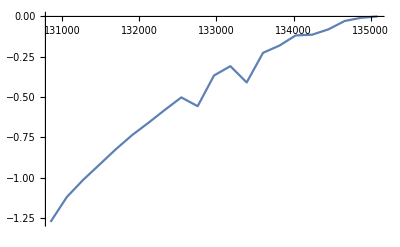

```mathematica
ListPlot[{EBgridf,bpalMax2}//Thread,Joined->True]
```

#### Taur

```mathematica
TaurconfigFB=ReadList["/Users/ingrid/Dropbox/MATHEMATICA/BunnefeldEtAl_Scripts/SpeciesMutationalConfigs/TaurconfigFB.txt"]
```

{SparseArray[<16>, {4, 4}],SparseArray[<16>, {4, 4}],SparseArray[<16>, {4, 4}],SparseArray[<16>, {4, 4}],SparseArray[<16>, {4, 4}],SparseArray[<16>, {4, 4}],SparseArray[<64>, {4, 4, 4}]}

```mathematica
taurCount=Total[Normal[TaurconfigFB[[1]]//Normal//Flatten]]
```

313373

```mathematica
taurBestModS=TransMods[[3]];
```

```mathematica
AbsoluteTiming[testtaurT2poly=ModelTabPoly[taurBestModS,TaurconfigFB,{1,2},TMgrid,{0.01,0.3},{0.01,0.3},2,150]]
```

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

{1171.78,{{-5.95127×10^6,{theta→1.56754,xx→0.0676535,yy→0.03559}},{-5.95127×10^6,{theta→1.56559,xx→0.0697914,yy→0.0370095}},{-5.95127×10^6,{theta→1.56373,xx→0.0708867,yy→0.039305}},{-5.95128×10^6,{theta→1.56172,xx→0.0727287,yy→0.0415658}},{-5.95129×10^6,{theta→1.55989,xx→0.0740935,yy→0.0430015}},{-5.9513×10^6,{theta→1.55809,xx→0.0754387,yy→0.044947}},{-5.95131×10^6,{theta→1.55616,xx→0.0770674,yy→0.0464736}},{-5.95132×10^6,{theta→1.55425,xx→0.0790591,yy→0.0479495}},{-5.95134×10^6,{theta→1.55239,xx→0.0800318,yy→0.0499045}},{-5.95136×10^6,{theta→1.5505,xx→0.0814725,yy→0.0515923}},{-5.95138×10^6,{theta→1.54866,xx→0.082975,yy→0.0533016}},{-5.9514×10^6,{theta→1.54676,xx→0.0843011,yy→0.0549552}},{-5.95143×10^6,{theta→1.54488,xx→0.0856947,yy→0.056496}},{-5.95145×10^6,{theta→1.54298,xx→0.0871084,yy→0.0581236}},{-5.95148×10^6,{theta→1.54112,xx→0.0883972,yy→0.0596345}},{-5.95151×10^6,{theta→1.53925,xx→0.0897346,yy→0.0611968}},{-5.95155×10^6,{theta→1.53738,xx→0.0910587,yy→0.0628509}},{-5.95158×10^6,{theta→1.53551,xx→0.0923353,yy→0.0642209}},{-5.95162×10^6,{theta→1.53349,xx→0.0936751,yy→0.0654377}},{-5.95166×10^6,{theta→1.53179,xx→0.09486,yy→0.0671659}},{-5.9517×10^6,{theta→1.52995,xx→0.0960875,yy→0.0685783}}}}

```mathematica
taurMax2=maxCurve[testtaurT2poly/taurCount,2000]
```

{0.,-0.00706993,-0.0279063,-0.0627038,-0.111194,-0.173547,-0.249664,-0.339584,-0.443164,-0.560494,-0.691518,-0.836207,-0.994547,-1.16652,-1.35209,-1.55125,-1.76398,-1.99026,-2.23011,-2.48336,-2.75016}

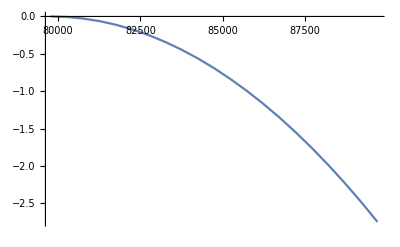

```mathematica
ListPlot[{TMgridf,taurMax2}//Thread,Joined->True]
```

#### Mdor

```mathematica
MdorconfigFB=ReadList["/Users/ingrid/Dropbox/MATHEMATICA/BunnefeldEtAl_Scripts/SpeciesMutationalConfigs/MdorconfigFB.txt"]
```

{SparseArray[<16>, {4, 4}],SparseArray[<16>, {4, 4}],SparseArray[<16>, {4, 4}],SparseArray[<16>, {4, 4}],SparseArray[<16>, {4, 4}],SparseArray[<16>, {4, 4}],SparseArray[<64>, {4, 4, 4}]}

```mathematica
mdorCount=Total[Normal[MdorconfigFB[[1]]//Normal//Flatten]]
```

228917

```mathematica
mdorBestModS=TransMods[[4]];
```

```mathematica
AbsoluteTiming[testmdorT2=ModelTAZTabT2x[mdorBestModS,MdorconfigFB,{0.5,1.5},{5000,15000},TMgrid,{4,7},{0.1,0.6},{0.2,0.6},2,200];]
```

```mathematica
testmdorT2={{-4.429340277621133*^6,{theta->1.2692917767664462,t1->10278.132467087911,xx->4.00125940118193,yy->0.3402056212595438,aa1->0.3546625775543125}},{-4.429290492925693*^6,{theta->1.2650106266211794,t1->10177.9299578766,xx->4.010403636077182,yy->0.3390700360813722,aa1->0.3568063516838412}},{-4.429242920918636*^6,{theta->1.2619149832682963,t1->10135.648539157426,xx->4.002994090539187,yy->0.3395997153643314,aa1->0.3610099119442949}},{-4.42919616983816*^6,{theta->1.2572718693986351,t1->10154.535372468334,xx->4.0007596535262575,yy->0.3387840740892805,aa1->0.3607302594772826}},{-4.429152346851705*^6,{theta->1.2531292484149326,t1->10096.15960797793,xx->4.000451144654438,yy->0.33997186103041344,aa1->0.3623192714670843}},{-4.429112711288377*^6,{theta->1.2500497640223025,t1->10106.9663194479,xx->4.,yy->0.34100763212589064,aa1->0.3612684910464375}},{-4.42907831748318*^6,{theta->1.2467192196444796,t1->10022.955390473586,xx->4.005638740766248,yy->0.3426794672234443,aa1->0.3595436468200889}},{-4.429036413528314*^6,{theta->1.2408003200027515,t1->9970.773020233295,xx->4.003397026527166,yy->0.33945600079625504,aa1->0.3667276880591416}},{-4.429001972982882*^6,{theta->1.2373697060313047,t1->9946.282145658162,xx->4.001046438969002,yy->0.3405991224491828,aa1->0.36886105560076976}},{-4.428970790122321*^6,{theta->1.2338571630158137,t1->9865.24590740956,xx->4.008471313237556,yy->0.34039094194990716,aa1->0.3718218378580494}},{-4.429014827921586*^6,{theta->1.2285597096470562,t1->8201.751255573046,xx->4.736926986150047,yy->0.33429209131284365,aa1->0.37058922569699015}},{-4.428913483184579*^6,{theta->1.224810937339115,t1->9765.710696487888,xx->4.017635404373593,yy->0.3392679869095563,aa1->0.3741602291980882}},{-4.42890375292289*^6,{theta->1.2214662784057153,t1->9375.61133534274,xx->4.173336458844595,yy->0.33869451907482917,aa1->0.37485190615134173}},{-4.428862812081367*^6,{theta->1.2175968289965107,t1->9766.105247646354,xx->4.002709541537631,yy->0.3394037250128528,aa1->0.37738427808510544}},{-4.429112776639193*^6,{theta->1.2072478107287268,t1->5269.192183495903,xx->6.999468253246915,yy->0.31862871406472504,aa1->0.3779782741736124}},{-4.428820762870668*^6,{theta->1.2084292725602768,t1->9665.06378182441,xx->4.0000312700177245,yy->0.33841738130059995,aa1->0.3814561953587937}},{-4.428803634507759*^6,{theta->1.206560491460769,t1->9656.07368403723,xx->4.000291160890299,yy->0.33980440033088644,aa1->0.38371149709953184}},{-4.428787950970544*^6,{theta->1.2003282836081008,t1->9564.166691400962,xx->4.0088213825035375,yy->0.33765239198012453,aa1->0.3852564677107815}},{-4.428906906878729*^6,{theta->1.1975305748918492,t1->7093.208316331724,xx->5.273788287468557,yy->0.3310509104324635,aa1->0.383188346751975}},{-4.428775129881389*^6,{theta->1.1897337275409783,t1->9347.936893274415,xx->4.082722841381098,yy->0.3379564960017467,aa1->0.38979226047313686}},{-4.428759603009402*^6,{theta->1.1867813545383579,t1->9501.720179143356,xx->4.030557225418327,yy->0.332251831105698,aa1->0.3913849171039327}}}
```

{{-4.42934×10^6,{theta→1.26929,t1→10278.1,xx→4.00126,yy→0.340206,aa1→0.354663}},{-4.42929×10^6,{theta→1.26501,t1→10177.9,xx→4.0104,yy→0.33907,aa1→0.356806}},{-4.42924×10^6,{theta→1.26191,t1→10135.6,xx→4.00299,yy→0.3396,aa1→0.36101}},{-4.4292×10^6,{theta→1.25727,t1→10154.5,xx→4.00076,yy→0.338784,aa1→0.36073}},{-4.42915×10^6,{theta→1.25313,t1→10096.2,xx→4.00045,yy→0.339972,aa1→0.362319}},{-4.42911×10^6,{theta→1.25005,t1→10107.,xx→4.,yy→0.341008,aa1→0.361268}},{-4.42908×10^6,{theta→1.24672,t1→10023.,xx→4.00564,yy→0.342679,aa1→0.359544}},{-4.42904×10^6,{theta→1.2408,t1→9970.77,xx→4.0034,yy→0.339456,aa1→0.366728}},{-4.429×10^6,{theta→1.23737,t1→9946.28,xx→4.00105,yy→0.340599,aa1→0.368861}},{-4.42897×10^6,{theta→1.23386,t1→9865.25,xx→4.00847,yy→0.340391,aa1→0.371822}},{-4.42901×10^6,{theta→1.22856,t1→8201.75,xx→4.73693,yy→0.334292,aa1→0.370589}},{-4.42891×10^6,{theta→1.22481,t1→9765.71,xx→4.01764,yy→0.339268,aa1→0.37416}},{-4.4289×10^6,{theta→1.22147,t1→9375.61,xx→4.17334,yy→0.338695,aa1→0.374852}},{-4.42886×10^6,{theta→1.2176,t1→9766.11,xx→4.00271,yy→0.339404,aa1→0.377384}},{-4.42911×10^6,{theta→1.20725,t1→5269.19,xx→6.99947,yy→0.318629,aa1→0.377978}},{-4.42882×10^6,{theta→1.20843,t1→9665.06,xx→4.00003,yy→0.338417,aa1→0.381456}},{-4.4288×10^6,{theta→1.20656,t1→9656.07,xx→4.00029,yy→0.339804,aa1→0.383711}},{-4.42879×10^6,{theta→1.20033,t1→9564.17,xx→4.00882,yy→0.337652,aa1→0.385256}},{-4.42891×10^6,{theta→1.19753,t1→7093.21,xx→5.27379,yy→0.331051,aa1→0.383188}},{-4.42878×10^6,{theta→1.18973,t1→9347.94,xx→4.08272,yy→0.337956,aa1→0.389792}},{-4.42876×10^6,{theta→1.18678,t1→9501.72,xx→4.03056,yy→0.332252,aa1→0.391385}}}

```mathematica
mdorMax2=maxCurve[testmdorT2/mdorCount,2000]
```

{-5.07323,-4.63827,-4.22265,-3.81419,-3.43132,-3.08503,-2.78454,-2.41844,-2.11754,-1.8451,-2.22985,-1.34442,-1.25941,-0.901716,-3.0856,-0.534341,-0.384694,-0.24767,-1.28696,-0.135655,0.}

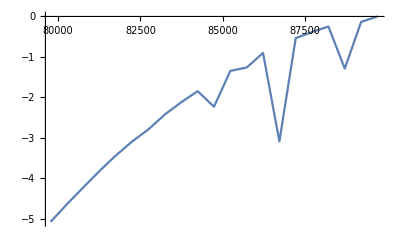

```mathematica
ListPlot[{TMgridf,mdorMax2}//Thread,Joined->True]
```

#### Ebru

```mathematica
EbruconfigFB=ReadList["/Users/ingrid/Dropbox/MATHEMATICA/BunnefeldEtAl_Scripts/SpeciesMutationalConfigs/EbruconfigFB.txt"];
```

```mathematica
ebruBestModS=TransMods[[6]];
```

```mathematica
AbsoluteTiming[testebruT2=ModelTAZTabT2x[ebruBestModS,EbruconfigFB,{2.1,3.5},{50000,90000},ENgrid,{0.01,0.5},{1,3},{0.5,1},2,150];]
```

```mathematica
testebruT2={{-1.1747928628360089*^7,{theta->3.4999999659926404,t1->71628.29794494149,xx->0.010066905755015667,yy->2.95632842921304,aa1->0.913926266231628}},{-1.1747958119472176*^7,{theta->3.4324785275852916,t1->71559.72595564974,xx->0.010296794769608982,yy->2.8982890514938497,aa1->0.9137265354115607}},{-1.1747957261444502*^7,{theta->3.4993702942611655,t1->72142.91191583837,xx->0.012900146126892812,yy->2.967758208349321,aa1->0.9138886023791637}},{-1.174793167129809*^7,{theta->3.4970131437892884,t1->71563.40496348747,xx->0.010601916968829277,yy->2.951532975262608,aa1->0.9152205937534109}},{-1.1747934482835859*^7,{theta->3.485158175816757,t1->71891.51652803656,xx->0.010000011425188016,yy->2.940809354898519,aa1->0.9160375864731796}},{-1.1747955956880663*^7,{theta->3.443629904281196,t1->71930.09623435134,xx->0.010050980292454093,yy->2.9103484331970346,aa1->0.9164705030957316}},{-1.1747941621511709*^7,{theta->3.48004094743048,t1->72209.27427878672,xx->0.010143344996658251,yy->2.941581058738538,aa1->0.9162922491783176}},{-1.1747952201615792*^7,{theta->3.4999871325344554,t1->72895.89341532193,xx->0.011770486569686711,yy->2.9647183210383234,aa1->0.9165417344439348}},{-1.1747943433452537*^7,{theta->3.4980447734992586,t1->72216.48911171654,xx->0.010219624399649626,yy->2.9556672562418482,aa1->0.9172510145330218}},{-1.1747949734790325*^7,{theta->3.4988278652905285,t1->72765.46137335018,xx->0.010332992174158943,yy->2.9573103272689987,aa1->0.9180997075443442}},{-1.1747957993352048*^7,{theta->3.497415980391543,t1->72902.91480001493,xx->0.010000003634784586,yy->2.960414616641456,aa1->0.9184597725003427}},{-1.1747969531368002*^7,{theta->3.482950376363565,t1->72613.78912949373,xx->0.010019888105913135,yy->2.945377988051772,aa1->0.9181439366044034}},{-1.1747976407070778*^7,{theta->3.4928122850785503,t1->72822.3705818952,xx->0.01093303437793467,yy->2.9519193653817295,aa1->0.9189389457490936}},{-1.1747991145962398*^7,{theta->3.465139324283194,t1->72800.41419062627,xx->0.01000066112449658,yy->2.9280481402779923,aa1->0.9195646438168037}},{-1.1748006535035059*^7,{theta->3.455234126231995,t1->72754.46618939568,xx->0.01034743665524994,yy->2.9169610160474932,aa1->0.9203610071632191}},{-1.1748015257291583*^7,{theta->3.4574394721297983,t1->72915.10542243958,xx->0.010324627619333936,yy->2.92162576146377,aa1->0.920628749931826}},{-1.1748059547344137*^7,{theta->3.4475578711875405,t1->73912.74950897325,xx->0.013476214725529508,yy->2.9231167909887055,aa1->0.9217539440052773}},{-1.1748020330561556*^7,{theta->3.5,t1->73517.67569579041,xx->0.01041096203992919,yy->2.962204453648506,aa1->0.9214438466017782}},{-1.1748033052771192*^7,{theta->3.494156690374279,t1->73610.75290123167,xx->0.010134077091920803,yy->2.959013730144866,aa1->0.9214217062692964}},{-1.1748042930624496*^7,{theta->3.4990123217536624,t1->74291.50997150816,xx->0.010190361661933975,yy->2.964500862594317,aa1->0.9221643341335023}},{-1.1748056039792854*^7,{theta->3.4984317232003166,t1->74102.83312239016,xx->0.010403484444093754,yy->2.9628420476764337,aa1->0.9222502417442069}}}
```

```mathematica
ebruCount=Total[Normal[EbruconfigFB[[1]]//Normal//Flatten]]
```

```mathematica
ebruCount=659990
```

659990

```mathematica
ebruMax2=maxCurve[testebruT2/ebruCount,2000]
```

{0.,-0.0893684,-0.0867682,-0.00922116,-0.0177411,-0.082815,-0.0393738,-0.0714352,-0.0448646,-0.0639598,-0.0889862,-0.12395,-0.144786,-0.18945,-0.236084,-0.262516,-0.39673,-0.27789,-0.316442,-0.346376,-0.386101}

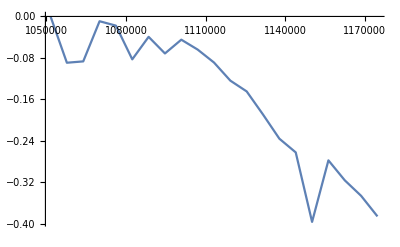

```mathematica
ListPlot[{ENgridf,ebruMax2}//Thread,Joined->True]
```

(Proceed, curve not smooth because of wide CIs on Ebru, support for whole ENgrid is similar)

#### Neuqba

```mathematica
NeuqbaconfigFB=ReadList["/Users/ingrid/Dropbox/MATHEMATICA/BunnefeldEtAl_Scripts/SpeciesMutationalConfigs/NeuqbaconfigFB.txt"];
```

```mathematica
neuqbaCount=Total[Normal[NeuqbaconfigFB[[1]]//Normal//Flatten]]
```

397148

```mathematica
neuqbaCount=397148
```

397148

```mathematica
neuqbaBestModS=TransMods[[13]];
```

```mathematica
AbsoluteTiming[testneuqbaT2=ModelT1ZTabT2xx[neuqbaBestModS,NeuqbaconfigFB,{0.2,0.6},ENgrid,{1,2},{0.1,1},{130000,200000},{0.2,1},2,150];]
```

```mathematica
testneuqbaT2={{-6.073596331544148*^6,{theta->0.2530789364602216,xx->1.0795075012722746,yy->0.48144130453237177,admm->130000.,aa1->0.29250414077205195}},{-6.072986953326233*^6,{theta->0.252053117941269,xx->1.096013554551419,yy->0.47994448368216086,admm->130000.,aa1->0.295119244626479}},{-6.072396408985708*^6,{theta->0.25174111352059514,xx->1.0832365732256233,yy->0.47473523794656847,admm->130285.87334227597,aa1->0.2985799154327311}},{-6.071783211825641*^6,{theta->0.248971131935717,xx->1.0642034930791457,yy->0.47156512876503853,admm->130052.55599431852,aa1->0.3006151517731359}},{-6.071241886579452*^6,{theta->0.2476215305095165,xx->1.0554957113661416,yy->0.46799673780786155,admm->130070.38078971594,aa1->0.30307527096542247}},{-6.070739675204886*^6,{theta->0.247412111935695,xx->1.0580934415312968,yy->0.4658877460144364,admm->130118.78584962751,aa1->0.3066131654137332}},{-6.070241976041927*^6,{theta->0.24420368993067282,xx->1.0440939966192588,yy->0.46166653741484587,admm->130019.78349385495,aa1->0.3083646751267808}},{-6.069786337538865*^6,{theta->0.24360025283515863,xx->1.0426221528573294,yy->0.4591772485607104,admm->130000.,aa1->0.3108631807616139}},{-6.069375362807075*^6,{theta->0.24263760321906913,xx->1.047377602596941,yy->0.4554417763375338,admm->130029.29286809429,aa1->0.31472541802757803}},{-6.069006864480534*^6,{theta->0.23850262779693562,xx->1.0009002944287788,yy->0.44900665305155046,admm->130000.,aa1->0.31567299217847444}},{-6.071008010200527*^6,{theta->0.2685607982930504,xx->1.121533924775217,yy->0.533489088573644,admm->145562.6614228269,aa1->0.3213357019820337}},{-6.068334415973598*^6,{theta->0.23674328715488047,xx->1.,yy->0.44301727938530727,admm->130149.95139695748,aa1->0.31684428292332145}},{-6.067956719311969*^6,{theta->0.23757889193524384,xx->1.0232230488949847,yy->0.4456308791419123,admm->130038.08694872621,aa1->0.3231854208786007}},{-6.068034729698608*^6,{theta->0.2294420473483586,xx->1.0024253757832007,yy->0.4385953484849645,admm->130409.01819488249,aa1->0.3298649284762683}},{-6.067421268000018*^6,{theta->0.23583942639114097,xx->1.0155628691962104,yy->0.4381599091345388,admm->130012.0331816267,aa1->0.3278084641462299}},{-6.0671915224237535*^6,{theta->0.2350761755097711,xx->1.0131170365365727,yy->0.43891557974035517,admm->130153.7920414725,aa1->0.33010932823223593}},{-6.067100787513324*^6,{theta->0.23901012441878478,xx->1.0381816882562316,yy->0.4448161085994805,admm->130991.18758762644,aa1->0.3347382720831113}},{-6.066841448833902*^6,{theta->0.23235738354279156,xx->1.0025069172387908,yy->0.4355732016991706,admm->130443.79910250282,aa1->0.3367402765369452}},{-6.066666230529603*^6,{theta->0.23272538591793107,xx->1.0133379145459231,yy->0.4324369105105217,admm->130053.30895422853,aa1->0.3385015430279012}},{-6.066518566475671*^6,{theta->0.23143949514756768,xx->1.000031529427408,yy->0.42940510906492163,admm->130006.22542299636,aa1->0.3394344459187072}},{-6.066422300515702*^6,{theta->0.23130651168917138,xx->1.0016799769638107,yy->0.429447201501178,admm->130000.,aa1->0.3412267168689828}}}
```

```mathematica
neuqbaMax2=maxCurve[testneuqbaT2/neuqbaCount,2000]
```

{-36.1277,-33.059,-30.085,-26.997,-24.271,-21.7419,-19.2355,-16.941,-14.8713,-13.0156,-23.0932,-9.62923,-7.72719,-8.12004,-5.03071,-3.87373,-3.4168,-2.11079,-1.22841,-0.484786,0.}

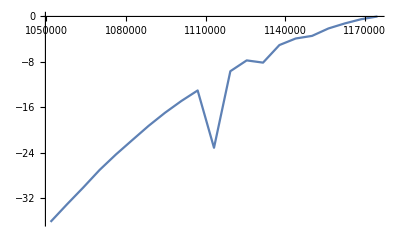

```mathematica
ListPlot[{ENgridf,neuqbaMax2}//Thread,Joined->True,PlotRange->All]
```

#### Testing Taur/Mdor cluster (briefly annotated)

```mathematica
ModelFitsTM={testtaurT2poly,testmdorT2};
```

```mathematica
T2countsTM={ taurCount,mdorCount}
```

{313373,228917}

```mathematica
speciesMax2=Table[maxCurve[ModelFitsTM[[i]]/T2countsTM[[i]],2000],{i,1,2}]
```

{{0.,-0.00706993,-0.0279063,-0.0627038,-0.111194,-0.173547,-0.249664,-0.339584,-0.443164,-0.560494,-0.691518,-0.836207,-0.994547,-1.16652,-1.35209,-1.55125,-1.76398,-1.99026,-2.23011,-2.48336,-2.75016},{-5.07323,-4.63827,-4.22265,-3.81419,-3.43132,-3.08503,-2.78454,-2.41844,-2.11754,-1.8451,-2.22985,-1.34442,-1.25941,-0.901716,-3.0856,-0.534341,-0.384694,-0.24767,-1.28696,-0.135655,0.}}

```mathematica
margalltabT2x=Table[{TMgridf,speciesMax2[[i]]}//Thread,{i,1,2}];
```

Fitting a quadratic equation to each set of points

```mathematica
TableForm[SetPrecision[bestfitquadtabT2=Table[Fit[margalltabT2x⟦i⟧,{1,x,x^2},x],{i,1,margalltabT2x//Length}],3], TableDepth->1]
```

-176.+0.00442 x-2.77×10^-8 x^2
-261.+0.00566 x-3.07×10^-8 x^2

Same, but constrained to hit the X axis

```mathematica
TableForm[SetPrecision[bestfitquadtabX=Table[FindFit[margalltabT2x⟦i⟧,-(b x-a)^2,{b,a},x],{i,1,margalltabT2x//Length}],3], TableDepth->1]
```

{b→0.000167,a→13.3}
{b→-0.000169,a→-15.7}

```mathematica
bestfitquadtabXEQT2=Table[-((bestfitquadtabX[[i]][[1]][[2]]*x-bestfitquadtabX[[i]][[2]][[2]])^2),{i,1,bestfitquadtabX//Length}]
```

{-(-13.2831+0.000166572 x)^2,-(15.7019-0.000169149 x)^2}

ListPlot::prng: Value of option PlotRange -> {{{79768.7,89702.7}},{-60,0}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

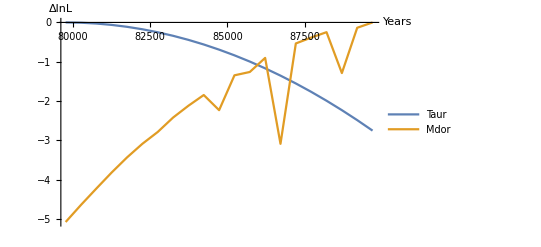

```mathematica
dataP=ListPlot[Table[{TMgridf,speciesMax2[[i]]}//Thread,{i,1,2}],Joined->True,AxesLabel->{"Years","ΔlnL"},PlotLegends->{"Taur","Mdor"},PlotRange->{{TM},{-60,0}}]
```

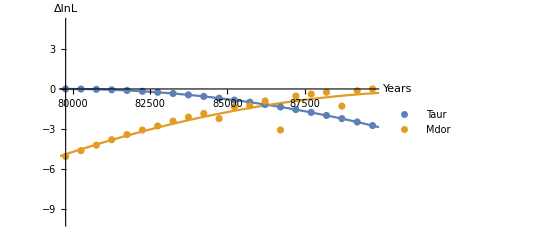

```mathematica
Show[{Plot[bestfitquadtabT2,{x,0,300000},AxesLabel->{"Years","ΔlnL"},PlotRange->{TM,{-10,5}}],ListPlot[margalltabT2x,PlotLegends->{"Taur","Mdor"},AxesLabel->{"Years","ΔlnL"}]}]
```

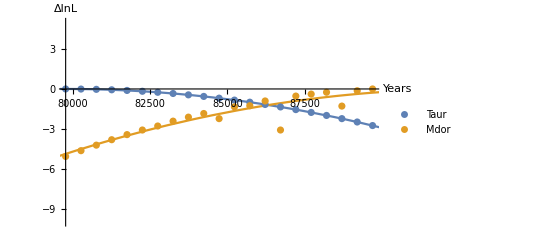

```mathematica
quadPX=Show[{Plot[bestfitquadtabXEQT2,{x,0,300000},AxesLabel->{"Years","ΔlnL"},PlotRange->{TM,{-10,5}}],ListPlot[margalltabT2x,PlotLegends->{"Taur","Mdor"},AxesLabel->{"Years","ΔlnL"}]}]
```

```mathematica
maxtT2=Table[Select[margalltabT2x[[i]],#[[2]]==0&][[1,1]],{i,1,2}]
```

{79768.7,89702.7}

```mathematica
TM
```

{79768.7,89702.7}

```mathematica
t2TabScaledTM=t2TabScaled[[{3,4}]];
```

These are the 95 % CIs either side of the maxima (using 2*SD of calibrated estimates from sim reps)

```mathematica
lowerCIT2KLb=Table[maxtT2⟦i⟧-(2*StandardDeviation[t2TabScaledTM⟦i⟧]),{i,1,2}];
upperCIT2KLb=Table[maxtT2⟦i⟧+(2*StandardDeviation[t2TabScaledTM⟦i⟧]),{i,1,2}];
```

Solving the best fit quadratic by working out what you would have to scale the curve by so that these 95 % CIs would give a delta lnL of - 2. Unconstrained:

```mathematica
lowercorrKLt2=Table[Solve[-2== y bestfitquadtabT2⟦i⟧/.x->lowerCIT2KLb⟦i⟧]⟦1,1,2⟧,{i,1,bestfitquadtabT2//Length}];
uppercorrKLt2=Table[Solve[-2== y bestfitquadtabT2⟦i⟧/.x->upperCIT2KLb⟦i⟧]⟦1,1,2⟧,{i,1,bestfitquadtabT2//Length}];
```

Constrained

```mathematica
lowercorrKLt2X=Table[Solve[-2== y bestfitquadtabXEQT2⟦i⟧/.x->lowerCIT2KLb⟦i⟧]⟦1,1,2⟧,{i,1,bestfitquadtabT2//Length}];
uppercorrKLt2X=Table[Solve[-2== y bestfitquadtabXEQT2⟦i⟧/.x->upperCIT2KLb⟦i⟧]⟦1,1,2⟧,{i,1,bestfitquadtabT2//Length}];
```

```mathematica
{lowerCIT2KLb, upperCIT2KLb} // Thread//TableForm
```

75404.3 | 84133.
75493.5 | 103912.

So, these are the correction factors - values closer to zero flatten the curve more ...
Negative values should not be allowed, but come about at the moment as we don' t currently force the best fit curve to hit its maximum at delta lnL = 0. Values above one indicate no correction needed.

```mathematica
{lowercorrKLt2, uppercorrKLt2} // Thread//TableForm
```

3.85691 | 3.74121
0.228842 | 0.464653

```mathematica
corrKLt2={lowercorrKLt2, uppercorrKLt2}//Thread
```

{{3.85691,3.74121},{0.228842,0.464653}}

```mathematica
{lowercorrKLt2X, uppercorrKLt2X} // Thread//TableForm
```

3.82735 | 3.74209
0.232608 | 0.56909

```mathematica
corrKLt2X={lowercorrKLt2X, uppercorrKLt2X}//Thread
```

{{3.82735,3.74209},{0.232608,0.56909}}

```mathematica
corrKLt2X={{1,1},{0.2326082800926578,0.5690903374016385}}
```

{{1.,1},{0.232608,0.56909}}

Proceeded with constrained estimates.

```mathematica
maxCurvesAllt2corrBx = Table[Min[corrKLt2X⟦i⟧]*speciesMax2⟦i⟧, {i, 1, speciesMax2 // Length}];
margalltabcorrt2MeanBx = Table[{TMgridf, maxCurvesAllt2corrBx[[i]]} // Thread, {i, 1, speciesMax2  // Length}];
```

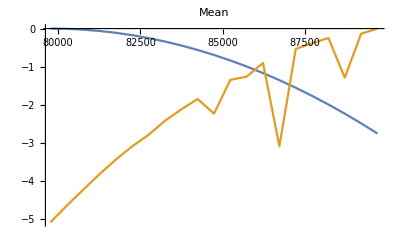

```mathematica
ListPlot[margalltabT2x, Joined->True,PlotLabel->"Mean",PlotRange->{{TM},{1,-40}}]
```

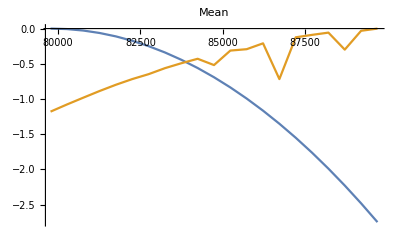

```mathematica
ListPlot[margalltabcorrt2MeanBx, Joined->True,PlotLabel->"Mean",PlotRange->{{TM},{1,-40}}]
```

```mathematica
sppl={"Taur","Mdor"}
```

{Taur,Mdor}

```mathematica
stepwisesimpTM=NestList[modelcrunchDOWN[#]&,{0,sppl,maxCurvesAllt2corrBx},1]
```

{{0,{Taur,Mdor},{{0.,-0.00706993,-0.0279063,-0.0627038,-0.111194,-0.173547,-0.249664,-0.339584,-0.443164,-0.560494,-0.691518,-0.836207,-0.994547,-1.16652,-1.35209,-1.55125,-1.76398,-1.99026,-2.23011,-2.48336,-2.75016},{-1.18008,-1.0789,-0.982223,-0.887213,-0.798154,-0.717604,-0.647707,-0.562548,-0.492556,-0.429185,-0.518681,-0.312723,-0.292949,-0.209747,-0.717737,-0.124292,-0.089483,-0.0576101,-0.299358,-0.0315545,0.}}},{-0.891151,{{Taur,Mdor}},{{-1.18008,-1.08597,-1.01013,-0.949917,-0.909347,-0.891151,-0.897372,-0.902132,-0.935721,-0.989679,-1.2102,-1.14893,-1.2875,-1.37626,-2.06983,-1.67555,-1.85347,-2.04787,-2.52947,-2.51492,-2.75016}}}}

```mathematica
tt={-1.1800759465515789,-1.0859709283470722,-1.0101291141109967,-0.9499166735488365,-0.9093472631337841,-0.8911509882542821,-0.8973716104367506,-0.9021319452797817,-0.9357207044650712,-0.9896790815501997,-1.2101992912701622,-1.1489302295488926,-1.2874955803770365,-1.3762624982494116,-2.069827998515273,-1.6755456988673783,-1.8534677823979266,-2.0478676500632402,-2.5294721030596694,-2.514918922000719,-2.7501572825698872}
```

{-1.18008,-1.08597,-1.01013,-0.949917,-0.909347,-0.891151,-0.897372,-0.902132,-0.935721,-0.989679,-1.2102,-1.14893,-1.2875,-1.37626,-2.06983,-1.67555,-1.85347,-2.04787,-2.52947,-2.51492,-2.75016}

```mathematica
Length[tt]
```

21

```mathematica
Max[tt]
```

-0.891151

```mathematica
Co-divergence time estimate
```

```mathematica
TMgridf[[6]]
```

82252.2

```mathematica
tt[[6]]
```

-0.891151

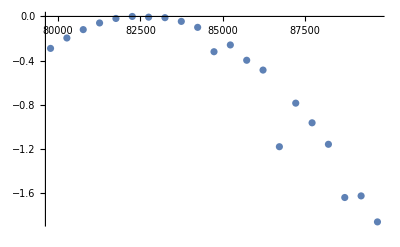

```mathematica
ListPlot[{TMgridf,tt-Max[tt]}//Thread]
```

```mathematica
TableForm[SetPrecision[#⟦{1,2}⟧&/@stepwisesimpTM,1],TableDepth->1]
```

{0,{Taur,Mdor}}
{-0.9,{{Taur,Mdor}}}

#### Testing Eann/Bpal cluster

```mathematica
ModelFitsEB={testeannT2,testbpalT2new};
```

```mathematica
T2countsEB={ eannCount,bpalCount}
```

{269892,265858}

```mathematica
speciesMax2=Table[maxCurve[ModelFitsEB[[i]]/T2countsEB[[i]],2000],{i,1,2}]
```

{{0.,-0.0893013,-0.184348,-0.285275,-0.392075,-0.504451,-0.62281,-0.746995,-0.876794,-1.01251,-1.15401,-1.3013,-1.45438,-1.61327,-1.77791,-1.94835,-5.52842,-5.69661,-2.49434,-2.68789,-2.88721},{-1.2732,-1.1186,-1.0123,-0.91768,-0.822429,-0.734551,-0.658199,-0.57841,-0.501637,-0.556044,-0.366007,-0.308008,-0.408839,-0.225341,-0.180647,-0.117529,-0.113105,-0.0798392,-0.0278534,-0.00825673,0.}}

```mathematica
margalltabT2x=Table[{EBgridf,speciesMax2[[i]]}//Thread,{i,1,2}];
```

Fitting a quadratic equation to each set of points (we need to constrain these to hit the x axis)

```mathematica
TableForm[SetPrecision[bestfitquadtabT2=Table[Fit[margalltabT2x⟦i⟧,{1,x,x^2},x],{i,1,margalltabT2x//Length}],3], TableDepth->1]
```

-1710.+0.0267 x-1.04×10^-7 x^2
-870.+0.0128 x-4.7×10^-8 x^2

Constrained to hit the X axis

```mathematica
TableForm[SetPrecision[bestfitquadtabX=Table[FindFit[margalltabT2x⟦i⟧,-(b x-a)^2,{b,a},x],{i,1,margalltabT2x//Length}],3], TableDepth->1]
```

{b→0.000399,a→51.8}
{b→-0.000229,a→-31.}

```mathematica
bestfitquadtabXEQT2=Table[-((bestfitquadtabX[[i]][[1]][[2]]*x-bestfitquadtabX[[i]][[2]][[2]])^2),{i,1,bestfitquadtabX//Length}]
```

{-(-51.835+0.000398532 x)^2,-(31.0275-0.00022863 x)^2}

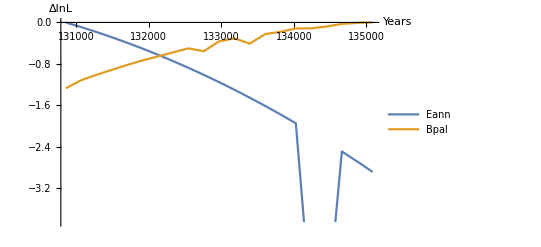

```mathematica
dataP=ListPlot[Table[{EBgridf,speciesMax2[[i]]}//Thread,{i,1,2}],Joined->True,AxesLabel->{"Years","ΔlnL"},PlotLegends->{"Eann","Bpal"},PlotRange->{{EB},{-60,0}}]
```

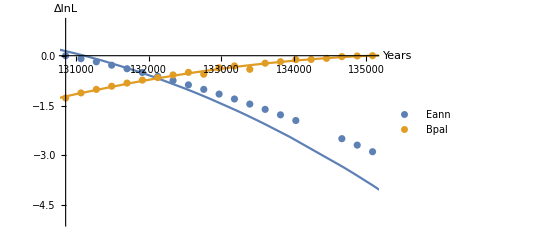

```mathematica
Show[{Plot[bestfitquadtabT2,{x,0,300000},AxesLabel->{"Years","ΔlnL"},PlotRange->{EB,{-5,1}}],ListPlot[margalltabT2x,PlotLegends->{"Eann","Bpal"},AxesLabel->{"Years","ΔlnL"}]}]
```

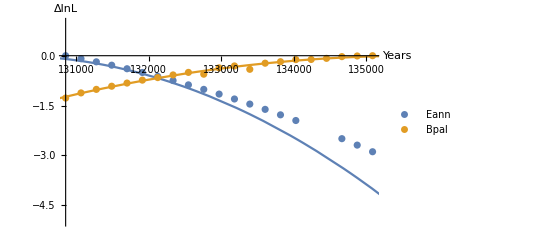

```mathematica
quadPX=Show[{Plot[bestfitquadtabXEQT2,{x,0,300000},AxesLabel->{"Years","ΔlnL"},PlotRange->{EB,{-5,1}}],ListPlot[margalltabT2x,PlotLegends->{"Eann","Bpal"},AxesLabel->{"Years","ΔlnL"}]}]
```

Constrained or not, looks very similar....

```mathematica
maxtT2=Table[Select[margalltabT2x[[i]],#[[2]]==0&][[1,1]],{i,1,2}]
```

{130854.,135086.}

```mathematica
EB
```

{130854.,135086.}

```mathematica
t2TabScaledEB=t2TabScaled[[{7,10}]];
```

These are the 95 % CIs either side of the maxima (using 2*SD of calibrated estimates from sim reps)

```mathematica
lowerCIT2KLb=Table[maxtT2⟦i⟧-(2*StandardDeviation[t2TabScaledEB[[i]]]),{i,1,2}];
upperCIT2KLb=Table[maxtT2⟦i⟧+(2*StandardDeviation[t2TabScaledEB⟦i⟧]),{i,1,2}];
```

Solving the best fit quadratic by working out what you would have to scale the curve by so that these 95 % CIs would give a delta lnL of - 2. Unconstrained:

```mathematica
lowercorrKLt2=Table[Solve[-2== y bestfitquadtabT2⟦i⟧/.x->lowerCIT2KLb⟦i⟧]⟦1,1,2⟧,{i,1,bestfitquadtabT2//Length}];
uppercorrKLt2=Table[Solve[-2== y bestfitquadtabT2⟦i⟧/.x->upperCIT2KLb⟦i⟧]⟦1,1,2⟧,{i,1,bestfitquadtabT2//Length}];
```

Constrained

```mathematica
lowercorrKLt2X=Table[Solve[-2== y bestfitquadtabXEQT2⟦i⟧/.x->lowerCIT2KLb⟦i⟧]⟦1,1,2⟧,{i,1,bestfitquadtabT2//Length}];
uppercorrKLt2X=Table[Solve[-2== y bestfitquadtabXEQT2⟦i⟧/.x->upperCIT2KLb⟦i⟧]⟦1,1,2⟧,{i,1,bestfitquadtabT2//Length}];
```

```mathematica
{lowerCIT2KLb, upperCIT2KLb} // Thread//TableForm
```

124582. | 137125.
126652. | 143519.

So, these are the correction factors - values closer to zero flatten the curve more ...
Negative values should not be allowed, but come about at the moment as we don' t currently force the best fit curve to hit its maximum at delta lnL = 0.

```mathematica
{lowercorrKLt2, uppercorrKLt2} // Thread//TableForm
```

2.71486 | 0.278914
0.487133 | 0.777167

```mathematica
corrKLt2={lowercorrKLt2, uppercorrKLt2}//Thread
```

{{2.71486,0.278914},{0.487133,0.777167}}

```mathematica
{lowercorrKLt2X, uppercorrKLt2X} // Thread//TableForm
```

0.418955 | 0.252622
0.466317 | 0.627561

```mathematica
corrKLt2X={lowercorrKLt2X, uppercorrKLt2X}//Thread
```

{{0.418955,0.252622},{0.466317,0.627561}}

```mathematica
maxCurvesAllt2corrBx = Table[Min[corrKLt2X⟦i⟧]*speciesMax2⟦i⟧, {i, 1, speciesMax2 // Length}];
margalltabcorrt2MeanBx = Table[{EBgridf, maxCurvesAllt2corrBx[[i]]} // Thread, {i, 1, speciesMax2  // Length}];
```

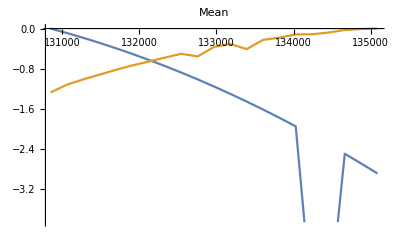

```mathematica
ListPlot[margalltabT2x, Joined->True,PlotLabel->"Mean",PlotRange->{{EB},{1,-40}}]
```

ListPlot::prng: Value of option PlotRange -> {{{130854.,135086.}},{1,-40}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

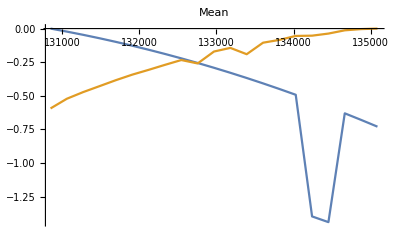

```mathematica
ListPlot[margalltabcorrt2MeanBx, Joined->True,PlotLabel->"Mean",PlotRange->{{EB},{1,-40}}]
```

```mathematica
sppl={"Eann","Bpal"}
```

{Eann,Bpal}

```mathematica
stepwisesimpEB=NestList[modelcrunchDOWN[#]&,{0,sppl,maxCurvesAllt2corrBx},1]
```

{{0,{Eann,Bpal},{{0.,-0.0225595,-0.0465705,-0.0720669,-0.0990468,-0.127435,-0.157336,-0.188707,-0.221498,-0.255782,-0.291529,-0.328737,-0.367409,-0.407548,-0.44914,-0.492197,-1.3966,-1.43909,-0.630125,-0.679022,-0.729373},{-0.593714,-0.52162,-0.472054,-0.42793,-0.383513,-0.342534,-0.306929,-0.269722,-0.233922,-0.259292,-0.170675,-0.143629,-0.190649,-0.10508,-0.0842386,-0.0548056,-0.0527426,-0.0372304,-0.0129885,-0.00385025,0.}}},{-0.455419,{{Eann,Bpal}},{{-0.593714,-0.54418,-0.518625,-0.499997,-0.482559,-0.469969,-0.464265,-0.45843,-0.455419,-0.515075,-0.462204,-0.472366,-0.558058,-0.512629,-0.533379,-0.547002,-1.44934,-1.47632,-0.643114,-0.682872,-0.729373}}}}

```mathematica
tt={-0.593713732467188,-0.5441798734270463,-0.5186245787838122,-0.4999966481259951,-0.4825593533232484,-0.4699689448968277,-0.46426472533218877,-0.45842995361072947,-0.4554193718462791,-0.5150747689823731,-0.46220390286394397,-0.47236624318455084,-0.5580578962221285,-0.5126287992621328,-0.5333786423605724,-0.5470022394281014,-1.4493428870606488,-1.4763200708267847,-0.6431135794135481,-0.6828717833845317,-0.7293731450299555}
```

{-0.593714,-0.54418,-0.518625,-0.499997,-0.482559,-0.469969,-0.464265,-0.45843,-0.455419,-0.515075,-0.462204,-0.472366,-0.558058,-0.512629,-0.533379,-0.547002,-1.44934,-1.47632,-0.643114,-0.682872,-0.729373}

```mathematica
EBgridf[[9]]
```

132546.

```mathematica
Max[tt]
```

-0.455419

```mathematica
tt[[9]]
```

-0.455419

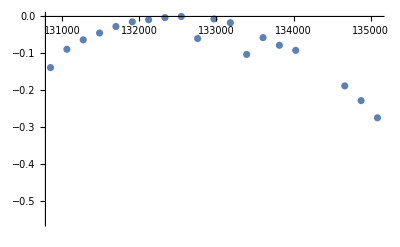

```mathematica
ListPlot[{EBgridf,tt-Max[tt]}//Thread]
```

```mathematica
TableForm[SetPrecision[#⟦{1,2}⟧&/@stepwisesimpEB,1],TableDepth->1]
```

{0,{Eann,Bpal}}
{-0.5,{{Eann,Bpal}}}

#### Testing Ebru/Neuqba cluster

```mathematica
ModelFitsEN={testebruT2,testneuqbaT2};
```

```mathematica
T2countsEN={ebruCount,neuqbaCount}
```

{659990,397148}

```mathematica
speciesMax2=Table[maxCurve[ModelFitsEN[[i]]/T2countsEN[[i]],2000],{i,1,2}]
```

{{0.,-0.0893684,-0.0867682,-0.00922116,-0.0177411,-0.082815,-0.0393738,-0.0714352,-0.0448646,-0.0639598,-0.0889862,-0.12395,-0.144786,-0.18945,-0.236084,-0.262516,-0.39673,-0.27789,-0.316442,-0.346376,-0.386101},{-36.1277,-33.059,-30.085,-26.997,-24.271,-21.7419,-19.2355,-16.941,-14.8713,-13.0156,-23.0932,-9.62923,-7.72719,-8.12004,-5.03071,-3.87373,-3.4168,-2.11079,-1.22841,-0.484786,0.}}

```mathematica
margalltabT2x=Table[{ENgridf,speciesMax2[[i]]}//Thread,{i,1,2}];
```

Fitting a quadratic equation to each set of points (we need to constrain these to hit the x axis)

```mathematica
TableForm[SetPrecision[bestfitquadtabT2=Table[Fit[margalltabT2x⟦i⟧,{1,x,x^2},x],{i,1,margalltabT2x//Length}],3], TableDepth->1]
```

-33.+0.0000622 x-2.93×10^-11 x^2
-1910.+0.00313 x-1.27×10^-9 x^2

Constrained to hit the X axis

```mathematica
TableForm[SetPrecision[bestfitquadtabX=Table[FindFit[margalltabT2x⟦i⟧,-(b x-a)^2,{b,a},x],{i,1,margalltabT2x//Length}],3], TableDepth->1]
```

{b→4.55×10^-6,a→4.71}
{b→-0.0000407,a→-48.8}

```mathematica
bestfitquadtabXEQT2=Table[-((bestfitquadtabX[[i]][[1]][[2]]*x-bestfitquadtabX[[i]][[2]][[2]])^2),{i,1,bestfitquadtabX//Length}]
```

{-(-4.71492+4.55231×10^-6 x)^2,-(48.8242-0.000040733 x)^2}

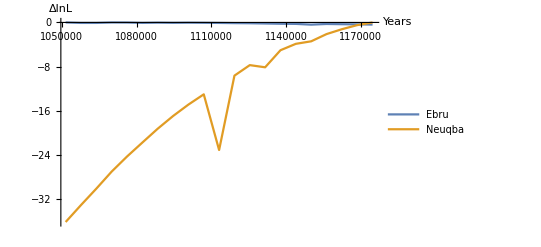

```mathematica
dataP=ListPlot[Table[{ENgridf,speciesMax2[[i]]}//Thread,{i,1,2}],Joined->True,AxesLabel->{"Years","ΔlnL"},PlotLegends->{"Ebru","Neuqba"}]
```

```mathematica
EN
```

EN

```mathematica
ENgridf
```

{1.05154×10^6,1.0577×10^6,1.06386×10^6,1.07002×10^6,1.07618×10^6,1.08234×10^6,1.0885×10^6,1.09466×10^6,1.10082×10^6,1.10699×10^6,1.11315×10^6,1.11931×10^6,1.12547×10^6,1.13163×10^6,1.13779×10^6,1.14395×10^6,1.15011×10^6,1.15627×10^6,1.16243×10^6,1.16859×10^6,1.17475×10^6}

```mathematica
Max[ENgridf]
```

1.17475×10^6

```mathematica
Min[ENgridf]
```

1.05154×10^6

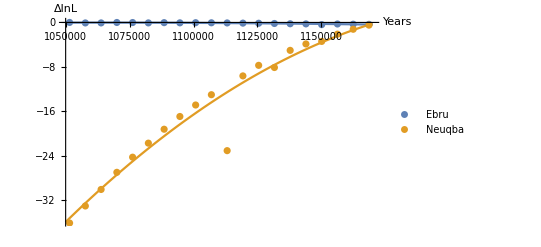

```mathematica
Show[{Plot[bestfitquadtabT2,{x,1.05*10^6,1.17*10^6},AxesLabel->{"Years","ΔlnL"}],ListPlot[margalltabT2x,PlotLegends->{"Ebru","Neuqba"},AxesLabel->{"Years","ΔlnL"}]}]
```

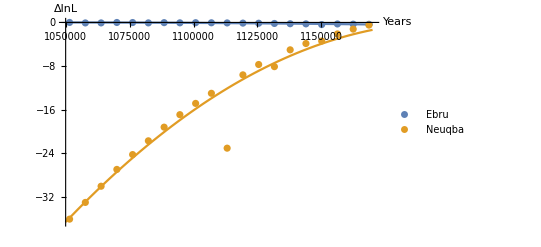

```mathematica
quadPX=Show[{Plot[bestfitquadtabXEQT2,{x,1.05*10^6,1.17*10^6},AxesLabel->{"Years","ΔlnL"}],ListPlot[margalltabT2x,PlotLegends->{"Ebru","Neuqba"},AxesLabel->{"Years","ΔlnL"}]}]
```

Constrained or not, looks very similar....

```mathematica
maxtT2=Table[Select[margalltabT2x[[i]],#[[2]]==0&][[1,1]],{i,1,2}]
```

{1.05154×10^6,1.17475×10^6}

These are really similar! Hooray!

```mathematica
t2TabScaledTM=t2TabScaled[[{5,13}]];
```

These are the 95 % CIs either side of the maxima (using 2*SD of calibrated estimates from sim reps)

```mathematica
lowerCIT2KLb=Table[maxtT2⟦i⟧-(2*StandardDeviation[t2TabScaledTM⟦i⟧]),{i,1,2}];
upperCIT2KLb=Table[maxtT2⟦i⟧+(2*StandardDeviation[t2TabScaledTM⟦i⟧]),{i,1,2}];
```

Solving the best fit quadratic by working out what you would have to scale the curve by so that these 95 % CIs would give a delta lnL of - 2. Unconstrained:

```mathematica
lowercorrKLt2=Table[Solve[-2== y bestfitquadtabT2⟦i⟧/.x->lowerCIT2KLb⟦i⟧]⟦1,1,2⟧,{i,1,bestfitquadtabT2//Length}];
uppercorrKLt2=Table[Solve[-2== y bestfitquadtabT2⟦i⟧/.x->upperCIT2KLb⟦i⟧]⟦1,1,2⟧,{i,1,bestfitquadtabT2//Length}];
```

Constrained

```mathematica
lowercorrKLt2X=Table[Solve[-2== y bestfitquadtabXEQT2⟦i⟧/.x->lowerCIT2KLb⟦i⟧]⟦1,1,2⟧,{i,1,bestfitquadtabT2//Length}];
uppercorrKLt2X=Table[Solve[-2== y bestfitquadtabXEQT2⟦i⟧/.x->upperCIT2KLb⟦i⟧]⟦1,1,2⟧,{i,1,bestfitquadtabT2//Length}];
```

```mathematica
{lowerCIT2KLb, upperCIT2KLb} // Thread//TableForm
```

1.05007×10^6 | 1.05301×10^6
1.15108×10^6 | 1.19843×10^6

So, these are the correction factors - values closer to zero flatten the curve more ...
Negative values should not be allowed, but come about at the moment as we don' t currently force the best fit curve to hit its maximum at delta lnL = 0.

```mathematica
{lowercorrKLt2, uppercorrKLt2} // Thread//TableForm
```

50.7184 | 52.9337
0.587925 | -0.693276

```mathematica
corrKLt2={lowercorrKLt2, uppercorrKLt2}//Thread
```

{{50.7184,52.9337},{0.587925,-0.693276}}

```mathematica
{lowercorrKLt2X, uppercorrKLt2X} // Thread//TableForm
```

468.518 | 322.949
0.532913 | 26482.2

```mathematica
corrKLt2X={lowercorrKLt2X, uppercorrKLt2X}//Thread
```

{{468.518,322.949},{0.532913,26482.2}}

```mathematica
corrKLt2X={{1,1},{0.5329128851821048,1}}
```

{{1.,1},{0.532913,1}}

```mathematica
maxCurvesAllt2corrBx = Table[Min[corrKLt2X⟦i⟧]*speciesMax2⟦i⟧, {i, 1, speciesMax2 // Length}];
margalltabcorrt2MeanBx = Table[{ENgridf, maxCurvesAllt2corrBx[[i]]} // Thread, {i, 1, speciesMax2  // Length}];
```

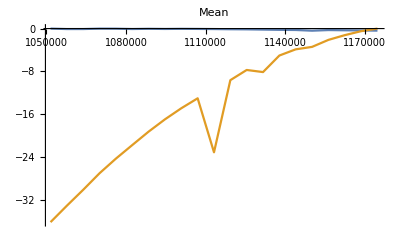

```mathematica
ListPlot[margalltabT2x, Joined->True,PlotLabel->"Mean"]
```

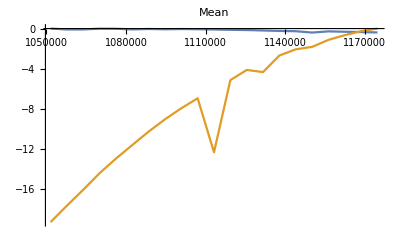

```mathematica
ListPlot[margalltabcorrt2MeanBx, Joined->True,PlotLabel->"Mean"]
```

```mathematica
sppl={"Ebru","Neuqba"}
```

{Ebru,Neuqba}

```mathematica
stepwisesimpEN=NestList[modelcrunchDOWN[#]&,{0,sppl,maxCurvesAllt2corrBx},1]
```

{{0,{Ebru,Neuqba},{{0.,-0.0893684,-0.0867682,-0.00922116,-0.0177411,-0.082815,-0.0393738,-0.0714352,-0.0448646,-0.0639598,-0.0889862,-0.12395,-0.144786,-0.18945,-0.236084,-0.262516,-0.39673,-0.27789,-0.316442,-0.346376,-0.386101},{-19.2529,-17.6176,-16.0327,-14.3871,-12.9343,-11.5865,-10.2509,-9.02806,-7.92513,-6.93619,-12.3067,-5.13154,-4.11792,-4.32727,-2.68093,-2.06436,-1.82086,-1.12487,-0.654635,-0.258349,0.}}},{-0.386101,{{Ebru,Neuqba}},{{-19.2529,-17.7069,-16.1195,-14.3963,-12.9521,-11.6693,-10.2902,-9.0995,-7.97,-7.00015,-12.3957,-5.25549,-4.2627,-4.51673,-2.91701,-2.32688,-2.21759,-1.40276,-0.971077,-0.604725,-0.386101}}}}

```mathematica
tt={-19.2529413405323,-17.70692186426781,-16.119478366058697,-14.39629456423222,-12.952060373944633,-11.669349958188777,-10.290233941932605,-9.09949866246204,-7.969995508770832,-7.000152096503779,-12.39565159056092,-5.255493113851132,-4.2627046633850405,-4.516725060361035,-2.917012649980474,-2.326876111331505,-2.2175852186993126,-1.4027576761860212,-0.9710771874410685,-0.6047246261971143,-0.3861011008226001}
```

{-19.2529,-17.7069,-16.1195,-14.3963,-12.9521,-11.6693,-10.2902,-9.0995,-7.97,-7.00015,-12.3957,-5.25549,-4.2627,-4.51673,-2.91701,-2.32688,-2.21759,-1.40276,-0.971077,-0.604725,-0.386101}

```mathematica
Length[tt]
```

21

```mathematica
ENgridf[[21]]
```

1.17475×10^6

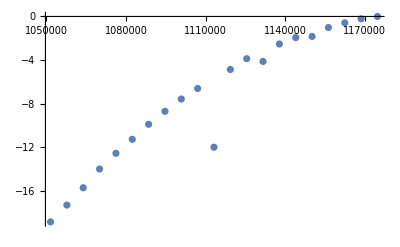

```mathematica
ListPlot[{ENgridf,tt-Max[tt]}//Thread]
```

```mathematica
TableForm[SetPrecision[#⟦{1,2}⟧&/@stepwisesimpEN,1],TableDepth->1]
```

{0,{Ebru,Neuqba}}
{-0.4,{{Ebru,Neuqba}}}

#### Is a model with these three pairs of species sharing divergence times significantly less likely than each species having their own divergence time?

```mathematica
TableForm[SetPrecision[#⟦{1,2}⟧&/@stepwisesimpTM,1],TableDepth->1]
```

{0,{Taur,Mdor}}
{-0.9,{{Taur,Mdor}}}

```mathematica
TableForm[SetPrecision[#⟦{1,2}⟧&/@stepwisesimpEB,1],TableDepth->1]
```

{0,{Eann,Bpal}}
{-0.5,{{Eann,Bpal}}}

```mathematica
TableForm[SetPrecision[#⟦{1,2}⟧&/@stepwisesimpEN,1],TableDepth->1]
```

{0,{Ebru,Neuqba}}
{-0.4,{{Ebru,Neuqba}}}

First cluster is "Ebru", "Neuqba"

```mathematica
0.4
```

Next is "Ebru", "Neuqba" & "Eann", "Bpal"

```mathematica
0.4+0.5
```

0.9

```mathematica
SetPrecision[1-CDF[ChiSquareDistribution[2],(2*0.9)],3]
```

0.407

Next is "Ebru", "Neuqba" & "Eann", "Bpal" & "Taur", "Mdor"

```mathematica
0.4+0.5+0.9
```

1.8

```mathematica
SetPrecision[1-CDF[ChiSquareDistribution[3],(2*1.8)],3]
```

0.308

No significant decline in log likelihood to assume these three pairs of species share divergence times

#### GF transformation functions

```mathematica
GFtransform[model_,block_,mu_,gen_]:=Module[{modelT,modelTT},
modelT=model/.T1->T1a-A1/.T2->(T2a-T1a)/.{A1->((realTAdm*block*mu)/(gen*0.5*theta)),T1a->((tt1*block*mu)/(gen*0.5*theta)),T2a->((realT2*block*mu)/(gen*0.5*theta))};
modelTT=Total[#]&/@(Table[Simplify[modelT[[i]],TimeConstraint->1],{i,1,7}])];
```

```mathematica
GFtransformNOADM[model_,block_,mu_,gen_]:=Module[{modelT,modelTT},
modelT=model/.T2->(T2a-T1)/.{T1->((tt1*block*mu)/(gen*0.5*theta)),T2a->((realT2*block*mu)/(gen*0.5*theta))};
modelTT=Total[#]&/@(Table[Simplify[modelT[[i]],TimeConstraint->1],{i,1,7}])];
```

```mathematica
GFtransformT1Z[model_,block_,mu_,gen_]:=Module[{modelT,modelTT},
modelT=model/.T2->(T2a-A1)/.{A1->((adm*block*mu)/(gen*0.5*theta)),T2a->((realT2*block*mu)/(gen*0.5*theta))};
modelTT=Total[#]&/@(Table[Simplify[modelT[[i]],TimeConstraint->1],{i,1,7}])];
```

```mathematica
GFtransformTAZ[model_,block_,mu_,gen_]:=Module[{modelT,modelTT},
modelT=model/.T2->(T2a-T1)/.{T1->((tt1*block*mu)/(gen*0.5*theta)),T2a->((realT2*block*mu)/(gen*0.5*theta))};
modelTT=Total[#]&/@(Table[Simplify[modelT[[i]],TimeConstraint->1],{i,1,7}])];
```

```mathematica
GFtransformPOLY[model_,block_,mu_,gen_]:=Module[{modelT,modelTT},
modelT=model/.T1->((tt1*block*mu)/(gen*0.5*theta));
modelTT=Total[#]&/@(Table[Simplify[modelT[[i]],TimeConstraint->1],{i,1,7}])];
```

#### Marginal likelihood curve fitting functions

Not all may be needed

```mathematica
ModelTabT2xx[model_,configs_,{θL_,θU_},{tt1L_,tt1U_},{tt2L_,tt2U_,s_},{xxL_,xxU_},{yyL_,yyU_},{admL_,admU_},{a1L_,a1U_},max_,iter_]:=ParallelTable[NMaximize[{Total[Table[totallnL[{model[[i]]},ω,theta,{λ[{x}]->xx,λ[{y}]->yy,realTAdm->adm,tt1->t1,a1->aa1},max,configs[[i]]],{i,1,7}]],yyU>yy>yyL,xxU>xx>xxL,realT2>t1>tt1L,θU>theta>θL,tt1L>adm>admL,a1U>aa1>a1L},{theta,t1,xx,yy,adm,aa1},MaxIterations->iter,Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}],{realT2,tt2L,tt2U,s}];
```

```mathematica
ModelTabPoly[model_,configs_,{θL_,θU_},{tt1L_,tt1U_,s_},{xxL_,xxU_},{yyL_,yyU_},max_,iter_]:=ParallelTable[NMaximize[{Total[Table[totallnL[{model[[i]]},ω,theta,{λ[{x}]->xx,λ[{y}]->yy},max,configs[[i]]],{i,1,7}]],yyU>yy>yyL,xxU>xx>xxL,θU>theta>θL},{theta,xx,yy},MaxIterations->iter,Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}],{tt1,tt1L,tt1U,s}];
```

```mathematica
ModelNOADTabT2[model_,configs_,{θL_,θU_},{tt1L_,tt1U_},{tt2L_,tt2U_,s_},{xxL_,xxU_},{yyL_,yyU_},max_,iter_]:=ParallelTable[NMaximize[{Total[Table[totallnL[{model[[i]]},ω,theta,{λ[{x}]->xx,λ[{y}]->yy,tt1->t1},max,configs[[i]]],{i,1,7}]],yyU>yy>yyL,xxU>xx>xxL,tt1U>t1>tt1L,θU>theta>θL},{theta,t1,xx,yy},MaxIterations->iter,Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}],{realT2,tt2L,tt2U,s}];
```

```mathematica
ModelNOADTabT2x[model_,configs_,{θL_,θU_},{tt1L_,tt1U_},{tt2L_,tt2U_,s_},{xxL_,xxU_},{yyL_,yyU_},max_,iter_]:=ParallelTable[NMaximize[{Total[Table[totallnL[{model[[i]]},ω,theta,{λ[{x}]->xx,λ[{y}]->yy,tt1->t1},max,configs[[i]]],{i,1,7}]],yyU>yy>yyL,xxU>xx>xxL,realT2>t1>tt1L,θU>theta>θL},{theta,t1,xx,yy},MaxIterations->iter,Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}],{realT2,tt2L,tt2U,s}];
```

```mathematica
ModelT1ZTabT2xx[model_,configs_,{θL_,θU_},{tt2L_,tt2U_,s_},{xxL_,xxU_},{yyL_,yyU_},{admL_,admU_},{a1L_,a1U_},max_,iter_]:=ParallelTable[NMaximize[{Total[Table[totallnL[{model[[i]]},ω,theta,{λ[{x}]->xx,λ[{y}]->yy,adm->admm,a1->aa1},max,configs[[i]]],{i,1,7}]],yyU>yy>yyL,xxU>xx>xxL,admU>admm>admL,θU>theta>θL,a1U>aa1>a1L},{theta,xx,yy,admm,aa1},MaxIterations->iter,Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}],{realT2,tt2L,tt2U,s}];
```

```mathematica
ModelT1ZTabT2x[model_,configs_,{θL_,θU_},{tt2L_,tt2U_,s_},{xxL_,xxU_},{yyL_,yyU_},{admL_,admU_},{a1L_,a1U_},max_,iter_]:=ParallelTable[NMaximize[{Total[Table[totallnL[{model[[i]]},ω,theta,{λ[{x}]->xx,λ[{y}]->yy,adm->admm,a1->aa1},max,configs[[i]]],{i,1,7}]],yyU>yy>yyL,xxU>xx>xxL,realT2>admm>admL,θU>theta>θL,a1U>aa1>a1L},{theta,xx,yy,admm,aa1},MaxIterations->iter,Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}],{realT2,tt2L,tt2U,s}];
```

```mathematica
ModelTAZTabT2x[model_,configs_,{θL_,θU_},{tt1L_,tt1U_},{tt2L_,tt2U_,s_},{xxL_,xxU_},{yyL_,yyU_},{a1L_,a1U_},max_,iter_]:=ParallelTable[NMaximize[{Total[Table[totallnL[{model[[i]]},ω,theta,{λ[{x}]->xx,λ[{y}]->yy,tt1->t1,a1->aa1},max,configs[[i]]],{i,1,7}]],yyU>yy>yyL,xxU>xx>xxL,realT2>t1>tt1L,θU>theta>θL,a1U>aa1>a1L},{theta,t1,xx,yy,aa1},MaxIterations->iter,Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}],{realT2,tt2L,tt2U,s}];
```

```mathematica
ModelTabT2x5[model_,configs_,{θL_,θU_},{tt1L_,tt1U_},{tt2L_,tt2U_,s_},{xxL_,xxU_},{yyL_,yyU_},{admL_,admU_},{a1L_,a1U_},max_,iter_,qq_,rr_]:=ParallelTable[NMaximize[{Total[Table[totallnL[{model[[i]]},ω,theta,{λ[{x}]->xx,λ[{y}]->yy,realTAdm->adm,tt1->t1,a1->aa1},max,configs[[i]]],{i,qq,rr}]],yyU>yy>yyL,xxU>xx>xxL,realT2>t1>tt1L,θU>theta>θL,admU>adm>admL,a1U>aa1>a1L},{theta,t1,xx,yy,adm,aa1},MaxIterations->iter,Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}],{realT2,tt2L,tt2U,s}];
```

```mathematica
ModelNOADTabT2x5[model_,configs_,{θL_,θU_},{tt1L_,tt1U_},{tt2L_,tt2U_,s_},{xxL_,xxU_},{yyL_,yyU_},max_,iter_,qq_,rr_]:=ParallelTable[NMaximize[{Total[Table[totallnL[{model[[i]]},ω,theta,{λ[{x}]->xx,λ[{y}]->yy,tt1->t1},max,configs[[i]]],{i,qq,rr}]],yyU>yy>yyL,xxU>xx>xxL,realT2>t1>tt1L,θU>theta>θL},{theta,t1,xx,yy},MaxIterations->iter,Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}],{realT2,tt2L,tt2U,s}];
```

```mathematica
ModelTAZTabT2x5[model_,configs_,{θL_,θU_},{tt1L_,tt1U_},{tt2L_,tt2U_,s_},{xxL_,xxU_},{yyL_,yyU_},{a1L_,a1U_},max_,iter_,qq_,rr_]:=ParallelTable[NMaximize[{Total[Table[totallnL[{model[[i]]},ω,theta,{λ[{x}]->xx,λ[{y}]->yy,tt1->t1,a1->aa1},max,configs[[i]]],{i,qq,7}]],yyU>yy>yyL,xxU>xx>xxL,tt1U>t1>tt1L,θU>theta>θL,a1U>aa1>a1L},{theta,t1,xx,yy,aa1},MaxIterations->iter,Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False,RandomSeed->4}],{realT2,tt2L,tt2U,s}];
```

#### Cluster functions

```mathematica
modelcrunchALLnew[spl_List,l_, k_]:=Module[{ll=l//Length,maxall,allpart, totclust,allres},allpart=KSetPartitions[ll,k]; 
maxall=Total[Max[#]&/@l];totclust=ParallelTable[Max[Total[l⟦#⟧]]&/@allpart⟦i⟧,{i,1,allpart//Length}];allres={(Total[#]&/@totclust),ParallelTable[spl⟦#⟧&/@allpart⟦i⟧,{i,1,allpart//Length}]}//Thread;(SortBy[allres,#⟦1⟧&]//Reverse)⟦1⟧];
```

```mathematica
modelcrunchDOWN[{lnL_,sppl_List,lnLl_List}]:=Module[{pairl, poslist=Range[Length[sppl]],maxl,bestpairpos,restlist,restmax},
pairl=Subsets[poslist,{2}];
maxl=Max[Total[lnLl⟦#⟧]]&/@pairl;
bestpairpos=pairl⟦Position[maxl,Max[maxl]]//Flatten⟧//Flatten;
restlist=Complement[poslist,bestpairpos];
restmax=Total[Max[#]&/@lnLl⟦restlist⟧];
{Max[maxl]+restmax,Append[sppl⟦restlist⟧,Flatten[sppl⟦bestpairpos⟧]],Append[lnLl⟦restlist⟧,Total[lnLl⟦bestpairpos⟧]]}]
```

## Fitting mixture distributions

### Species grid fitting

```mathematica
fullTransMods=Get["/home/lb57/Dropbox/Edinburgh_InUse/Genomics Lab/ReAnalysisSpring2017/bestModFull_FB_Mar17.m"];
```

#### Grid fitting functions

```mathematica
TinyFun[low_,high_]:=Table[i,{i,low,high,(high-low)/4}]
```

```mathematica
T1LIK[model_,configs_,theta1_,xx_,yy_,t1_,max_]:=Total[Table[totallnL[{model⟦i⟧/.{theta->theta1}},ω,theta1,{λ[{x}]->xx,λ[{y}]->yy,tt1->t1},max,configs⟦i⟧],{i,1,7}]]
```

```mathematica
oneDGrid[theta_,x_,y_,t1L_,t1U_,mod_,configs_]:=ParallelTable[{T1LIK[mod,configs,theta,x,y,t1grid,2],theta,x,y,t1grid},{t1grid,t1L,t1U,(t1U-t1L)/4}];
```

```mathematica
T1T2LIK[model_,configs_,theta1_,xx_,yy_,adm_,t1_,t2_,aa1_,max_]:=Total[Table[totallnL[{model⟦i⟧/.{theta->theta1}},ω,theta1,{λ[{x}]->xx,λ[{y}]->yy,realTAdm->adm,tt1->t1,realT2->t2,a1->aa1},max,configs⟦i⟧],{i,1,7}]]
```

```mathematica
twoDGrid[theta_,x_,y_,t1L_,t1U_,t2L_,t2U_,mod_,configs_]:=ParallelTable[{T1T2LIK[mod,configs,theta,x,y,0,t1grid,t2grid,0,2],theta,x,y,t1grid,t2grid},{t1grid,t1L,t1U,(t1U-t1L)/4},{t2grid,t2L,t2U,(t2U-t2L)/4}];
```

```mathematica
TAT1T2LIK5[model_,configs_,theta1_,xx_,yy_,adm_,t1_,t2_,aa1_,max_,trips_List]:=Total[Table[totallnL[{model⟦i⟧/.{theta->theta1}},ω,theta1,{λ[{x}]->xx,λ[{y}]->yy,realTAdm->adm,tt1->t1,realT2->t2,a1->aa1},max,configs⟦i⟧],{i,trips}]]
```

```mathematica
twoDGrid[theta_,x_,y_,t1L_,t1U_,t2L_,t2U_,mod_,configs_,trips_]:=ParallelTable[{TAT1T2LIK5[mod,configs,theta,x,y,0,t1grid,t2grid,0,2,trips],theta,x,y,t1grid,t2grid},{t1grid,t1L,t1U,(t1U-t1L)/4},{t2grid,t2L,t2U,(t2U-t2L)/4}];
```

```mathematica
fourDGrid[theta_,x_,y_,tadmL_,tadmU_,t1L_,t1U_,t2L_,t2U_,a1L_,a1U_,mod_,configs_]:=ParallelTable[{T1T2LIK[mod,configs,theta,x,y,tadmgrid,t1grid,t2grid,a1grid,2],theta,x,y,tadmgrid,t1grid,t2grid,a1grid},{tadmgrid,tadmL,tadmU,(tadmU-tadmL)/4},{t1grid,t1L,t1U,(t1U-t1L)/4},{t2grid,t2L,t2U,(t2U-t2L)/4},{a1grid,a1L,a1U,(a1U-a1L)/4}];
```

```mathematica
fourDGrid[theta_,x_,y_,tadmL_,tadmU_,t1L_,t1U_,t2L_,t2U_,a1L_,a1U_,mod_,configs_,trips_]:=ParallelTable[{TAT1T2LIK5[mod,configs,theta,x,y,tadmgrid,t1grid,t2grid,a1grid,2,trips],theta,x,y,tadmgrid,t1grid,t2grid,a1grid},{tadmgrid,tadmL,tadmU,(tadmU-tadmL)/4},{t1grid,t1L,t1U,(t1U-t1L)/4},{t2grid,t2L,t2U,(t2U-t2L)/4},{a1grid,a1L,a1U,(a1U-a1L)/4}];
```

#### Mdor

```mathematica
MdorconfigFB=ReadList["/Users/ingrid/Dropbox/MATHEMATICA/BunnefeldEtAl_Scripts/SpeciesMutationalConfigs/MdorconfigFB.txt"];
```

```mathematica
mdorCount=Total[Normal[MdorconfigFB[[1]]//Normal//Flatten]]
```

228917

```mathematica
mdorBestModF=fullTransMods[[4]];
```

(Best model params, uncalibrated)

```mathematica
mdorBestF=mdorO[[6]]
```

{-4.42881×10^6,{theta→1.19002,t1→0.0725104,t2→0.71158,adm→1.16503×10^-6,aa→0.389329,yy→0.333081,xx→4.5368}}

Here generating the 4 D grid (T1, T2, Tadm, f)

```mathematica
(upperCIT1[[4]]-lowerCIT1[[4]])
```

9818.37

```mathematica
AbsoluteTiming[mdor4D=fourDGrid [thetaBest[[4]],xScaleBest[[4]],yScaleBest[[4]],0,(upperCIT1[[4]]-lowerCIT1[[4]])/4,lowerCIT1[[4]],upperCIT1[[4]],lowerCIT2[[4]],upperCIT2[[4]],lowerF[[4]],upperF[[4]], mdorBestModF,MdorconfigFB];]
```

{2921.68,Null}

#### Cfun

```mathematica
CfunconfigFB=ReadList["/Users/ingrid/Dropbox/MATHEMATICA/BunnefeldEtAl_Scripts/SpeciesMutationalConfigs/CfunconfigFB.txt"];
```

```mathematica
cfunCount=Total[Normal[CfunconfigFB[[1]]//Normal//Flatten]]
```

388608

```mathematica
cfunBestModF=fullTransMods[[2]];
```

```mathematica
AbsoluteTiming[cfun4D=fourDGrid [thetaBest[[2]],xScaleBest[[2]],yScaleBest[[2]],lowerCITadm[[2]],upperCITadm[[2]],lowerCIT1[[2]],upperCIT1[[2]],lowerCIT2[[2]],upperCIT2[[2]],lowerF[[2]],upperF[[2]], cfunBestModF,CfunconfigFB];]
```

#### Sumb

```mathematica
SumbconfigFB=ReadList["/Users/ingrid/Dropbox/MATHEMATICA/BunnefeldEtAl_Scripts/SpeciesMutationalConfigs/SumbconfigFB.txt"];
```

```mathematica
sumbCount=Total[Normal[SumbconfigFB[[1]]//Normal//Flatten]]
```

300705

```mathematica
sumbBestModF=fullTransMods[[8]];
```

```mathematica
AbsoluteTiming[sumb4D=fourDGrid [thetaBest[[8]],xScaleBest[[8]],yScaleBest[[8]],lowerCITadm[[8]],upperCITadm[[8]],lowerCIT1[[8]],upperCIT1[[8]],lowerCIT2[[8]],upperCIT2[[8]],lowerF[[8]],upperF[[8]], sumbBestModF,SumbconfigFB,{1,2,3,4,7}];]
```

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

{5267.64,Null}

#### Neuqba

```mathematica
neuqbaBestModF=fullTransMods[[13]];
```

```mathematica
NeuqbaconfigFB=ReadList["/Users/ingrid/Dropbox/MATHEMATICA/BunnefeldEtAl_Scripts/SpeciesMutationalConfigs/NeuqbaconfigFB.txt"];
```

```mathematica
neuqbaCount=Total[Normal[NeuqbaconfigFB[[1]]//Normal//Flatten]]
```

397148

```mathematica
AbsoluteTiming[neuqba4D=fourDGrid [thetaBest[[13]],xScaleBest[[13]],yScaleBest[[13]],lowerCITadm[[13]],upperCITadm[[13]],lowerCIT1[[13]],upperCIT1[[13]],lowerCIT2[[13]],upperCIT2[[13]],lowerF[[13]],upperF[[13]], neuqbaBestModF,NeuqbaconfigFB];]
```

{2929.9,Null}

#### Ebru

```mathematica
EbruconfigFB=ReadList["/Users/ingrid/Dropbox/MATHEMATICA/BunnefeldEtAl_Scripts/SpeciesMutationalConfigs/EbruconfigFB.txt"];
```

```mathematica
ebruBestModF=fullTransMods[[6]];
```

```mathematica
ebruCount=Total[Normal[EbruconfigFB[[1]]//Normal//Flatten]]
```

659990

```mathematica
AbsoluteTiming[ebru4D=fourDGrid [thetaBest[[6]],xScaleBest[[6]],yScaleBest[[6]],0,(upperCIT1[[6]]-lowerCIT1[[6]]),lowerCIT1[[6]],upperCIT1[[6]],lowerCIT2[[6]],upperCIT2[[6]],lowerF[[6]],upperF[[6]], ebruBestModF,EbruconfigFB];]
```

#### Andgro

```mathematica
andgroBestModF=fullTransMods[[12]];
```

```mathematica
AndgroconfigFB=ReadList["/Users/ingrid/Dropbox/MATHEMATICA/BunnefeldEtAl_Scripts/SpeciesMutationalConfigs/AndgroconfigFB.txt"];
```

```mathematica
AbsoluteTiming[andgro4D=fourDGrid [thetaBest[[12]],xScaleBest[[12]],yScaleBest[[12]],lowerCITadm[[12]],upperCITadm[[12]],lowerCIT1[[12]],upperCIT1[[12]],lowerCIT2[[12]],upperCIT2[[12]],lowerF[[12]],upperF[[12]],andgroBestModF,AndgroconfigFB];]
```

{1440.62,Null}

```mathematica
andgroCount=Total[Normal[AndgroconfigFB[[1]]//Normal//Flatten]]
```

83489

#### Bpal

```mathematica
bpalBestModF=fullTransMods[[10]];
```

```mathematica
BpalconfigFB=ReadList["/Users/ingrid/Dropbox/MATHEMATICA/BunnefeldEtAl_Scripts/SpeciesMutationalConfigs/BpalconfigFB.txt"]
```

{SparseArray[<4>, {4, 4}],SparseArray[<4>, {4, 4}],SparseArray[<16>, {4, 4}],SparseArray[<16>, {4, 4}],SparseArray[<16>, {4, 4}],SparseArray[<16>, {4, 4}],SparseArray[<64>, {4, 4, 4}]}

```mathematica
AbsoluteTiming[bpal4D=fourDGrid [thetaBest[[10]],xScaleBest[[10]],yScaleBest[[10]],0,(upperCIT1[[10]]-lowerCIT1[[10]])/4,lowerCIT1[[10]],upperCIT1[[10]],lowerCIT2[[10]],upperCIT2[[10]],lowerF[[10]],upperF[[10]],bpalBestModF,BpalconfigFB,{3,4,5,6,7}];]
```

{491.383,Null}

```mathematica
bpalCount=Flatten[Normal[BpalconfigFB[[1]]]]//Total
```

265857

#### Onit

```mathematica
OnitconfigFB=ReadList["/Users/ingrid/Dropbox/MATHEMATICA/BunnefeldEtAl_Scripts/SpeciesMutationalConfigs/OnitconfigFB.txt"];
```

```mathematica
onitCount=Total[Normal[OnitconfigFB[[1]]//Normal//Flatten]]
```

193444

```mathematica
onitBestModF=fullTransMods[[1]];
```

```mathematica
onit2D=twoDGrid[thetaBest[[1]],xScaleBest[[1]],yScaleBest[[1]],lowerCIT1[[1]],upperCIT1[[1]],lowerCIT2[[1]],upperCIT2[[1]], onitBestModF,OnitconfigFB];
```

#### Eann

```mathematica
EannconfigFB=ReadList["/Users/ingrid/Dropbox/MATHEMATICA/BunnefeldEtAl_Scripts/SpeciesMutationalConfigs/EannconfigFB.txt"];
```

```mathematica
eannCount=Total[Normal[EannconfigFB[[1]]//Normal//Flatten]]
```

269892

```mathematica
eannBestModF=fullTransMods[[7]];
```

```mathematica
eann2D=twoDGrid[thetaBest[[7]],xScaleBest[[7]],yScaleBest[[7]],lowerCIT1[[7]],upperCIT1[[7]],lowerCIT2[[7]],upperCIT2[[7]], eannBestModF,EannconfigFB]
```

{{{-5.0696×10^6,0.951968,0.38358,0.189161,25972.8,124582.},{-5.0691×10^6,0.951968,0.38358,0.189161,25972.8,127718.},{-5.06895×10^6,0.951968,0.38358,0.189161,25972.8,130854.},{-5.06914×10^6,0.951968,0.38358,0.189161,25972.8,133989.},{-5.06966×10^6,0.951968,0.38358,0.189161,25972.8,137125.}},{{-5.06865×10^6,0.951968,0.38358,0.189161,33621.7,124582.},{-5.06825×10^6,0.951968,0.38358,0.189161,33621.7,127718.},{-5.06818×10^6,0.951968,0.38358,0.189161,33621.7,130854.},{-5.06845×10^6,0.951968,0.38358,0.189161,33621.7,133989.},{-5.06905×10^6,0.951968,0.38358,0.189161,33621.7,137125.}},{{-5.0682×10^6,0.951968,0.38358,0.189161,41270.6,124582.},{-5.06788×10^6,0.951968,0.38358,0.189161,41270.6,127718.},{-5.0679×10^6,0.951968,0.38358,0.189161,41270.6,130854.},{-5.06825×10^6,0.951968,0.38358,0.189161,41270.6,133989.},{-5.06894×10^6,0.951968,0.38358,0.189161,41270.6,137125.}},{{-5.06818×10^6,0.951968,0.38358,0.189161,48919.5,124582.},{-5.06795×10^6,0.951968,0.38358,0.189161,48919.5,127718.},{-5.06805×10^6,0.951968,0.38358,0.189161,48919.5,130854.},{-5.0685×10^6,0.951968,0.38358,0.189161,48919.5,133989.},{-5.06926×10^6,0.951968,0.38358,0.189161,48919.5,137125.}},{{-5.06855×10^6,0.951968,0.38358,0.189161,56568.4,124582.},{-5.0684×10^6,0.951968,0.38358,0.189161,56568.4,127718.},{-5.0686×10^6,0.951968,0.38358,0.189161,56568.4,130854.},{-5.06913×10^6,0.951968,0.38358,0.189161,56568.4,133989.},{-5.06999×10^6,0.951968,0.38358,0.189161,56568.4,137125.}}}

#### Opom

```mathematica
OpomconfigFB=ReadList["/Users/ingrid/Dropbox/MATHEMATICA/BunnefeldEtAl_Scripts/SpeciesMutationalConfigs/OpomconfigFB.txt"];
```

```mathematica
opomCount=Total[Normal[OpomconfigFB[[1]]//Normal//Flatten]]
```

588221

```mathematica
opomBestModF=fullTransMods[[9]];
```

```mathematica
opom2D=twoDGrid[thetaBest[[9]],xScaleBest[[9]],yScaleBest[[9]],lowerCIT1[[9]],upperCIT1[[9]],lowerCIT2[[9]],upperCIT2[[9]], opomBestModF,OpomconfigFB,{3,4,5,6,7}]
```

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

{{{-7.95428×10^6,0.636162,0.592071,0.251868,100633.,215596.},{-7.95443×10^6,0.636162,0.592071,0.251868,100633.,216282.},{-7.95458×10^6,0.636162,0.592071,0.251868,100633.,216968.},{-7.95475×10^6,0.636162,0.592071,0.251868,100633.,217654.},{-7.95492×10^6,0.636162,0.592071,0.251868,100633.,218340.}},{{-7.95421×10^6,0.636162,0.592071,0.251868,101416.,215596.},{-7.95435×10^6,0.636162,0.592071,0.251868,101416.,216282.},{-7.95451×10^6,0.636162,0.592071,0.251868,101416.,216968.},{-7.95467×10^6,0.636162,0.592071,0.251868,101416.,217654.},{-7.95484×10^6,0.636162,0.592071,0.251868,101416.,218340.}},{{-7.95414×10^6,0.636162,0.592071,0.251868,102198.,215596.},{-7.95428×10^6,0.636162,0.592071,0.251868,102198.,216282.},{-7.95444×10^6,0.636162,0.592071,0.251868,102198.,216968.},{-7.9546×10^6,0.636162,0.592071,0.251868,102198.,217654.},{-7.95477×10^6,0.636162,0.592071,0.251868,102198.,218340.}},{{-7.95407×10^6,0.636162,0.592071,0.251868,102981.,215596.},{-7.95422×10^6,0.636162,0.592071,0.251868,102981.,216282.},{-7.95437×10^6,0.636162,0.592071,0.251868,102981.,216968.},{-7.95453×10^6,0.636162,0.592071,0.251868,102981.,217654.},{-7.9547×10^6,0.636162,0.592071,0.251868,102981.,218340.}},{{-7.95402×10^6,0.636162,0.592071,0.251868,103764.,215596.},{-7.95416×10^6,0.636162,0.592071,0.251868,103764.,216282.},{-7.95431×10^6,0.636162,0.592071,0.251868,103764.,216968.},{-7.95447×10^6,0.636162,0.592071,0.251868,103764.,217654.},{-7.95464×10^6,0.636162,0.592071,0.251868,103764.,218340.}}}

#### Neusal

```mathematica
neusalBestModF=fullTransMods[[11]];
```

```mathematica
NeusalconfigFB=ReadList["/Users/ingrid/Dropbox/MATHEMATICA/BunnefeldEtAl_Scripts/SpeciesMutationalConfigs/NeusalconfigFB250.txt"];
```

```mathematica
neusal2D=twoDGrid[thetaBest[[11]],xScaleBest[[11]],yScaleBest[[11]],lowerCIT1[[11]],upperCIT1[[11]],lowerCIT2[[11]],upperCIT2[[11]], neusalBestModF,NeusalconfigFB]
```

{{{-1.22397×10^6,0.386468,4.59823,0.309629,53692.8,456586.},{-1.22402×10^6,0.386468,4.59823,0.309629,53692.8,465515.},{-1.22417×10^6,0.386468,4.59823,0.309629,53692.8,474443.},{-1.2244×10^6,0.386468,4.59823,0.309629,53692.8,483372.},{-1.22472×10^6,0.386468,4.59823,0.309629,53692.8,492301.}},{{-1.22333×10^6,0.386468,4.59823,0.309629,59783.2,456586.},{-1.22339×10^6,0.386468,4.59823,0.309629,59783.2,465515.},{-1.22354×10^6,0.386468,4.59823,0.309629,59783.2,474443.},{-1.22377×10^6,0.386468,4.59823,0.309629,59783.2,483372.},{-1.22409×10^6,0.386468,4.59823,0.309629,59783.2,492301.}},{{-1.2232×10^6,0.386468,4.59823,0.309629,65873.5,456586.},{-1.22326×10^6,0.386468,4.59823,0.309629,65873.5,465515.},{-1.22341×10^6,0.386468,4.59823,0.309629,65873.5,474443.},{-1.22365×10^6,0.386468,4.59823,0.309629,65873.5,483372.},{-1.22397×10^6,0.386468,4.59823,0.309629,65873.5,492301.}},{{-1.22345×10^6,0.386468,4.59823,0.309629,71963.8,456586.},{-1.22351×10^6,0.386468,4.59823,0.309629,71963.8,465515.},{-1.22366×10^6,0.386468,4.59823,0.309629,71963.8,474443.},{-1.2239×10^6,0.386468,4.59823,0.309629,71963.8,483372.},{-1.22422×10^6,0.386468,4.59823,0.309629,71963.8,492301.}},{{-1.22398×10^6,0.386468,4.59823,0.309629,78054.1,456586.},{-1.22404×10^6,0.386468,4.59823,0.309629,78054.1,465515.},{-1.22419×10^6,0.386468,4.59823,0.309629,78054.1,474443.},{-1.22442×10^6,0.386468,4.59823,0.309629,78054.1,483372.},{-1.22475×10^6,0.386468,4.59823,0.309629,78054.1,492301.}}}

```mathematica
neusalCount=((Flatten[Normal[#]]//Total)&/@NeusalconfigFB)//Mean//N
```

78015.7

#### Msti

```mathematica
MsticonfigFB=ReadList["/Users/ingrid/Dropbox/MATHEMATICA/BunnefeldEtAl_Scripts/SpeciesMutationalConfigs/MsticonfigFB.txt"];
```

```mathematica
mstiBestModF=fullTransMods[[5]];
```

```mathematica
mstiBestModS=TransMods[[5]];
```

```mathematica
msti1D=oneDGrid[thetaBest[[5]],xScaleBest[[5]],yScaleBest[[5]],lowerCIT1[[5]],upperCIT1[[5]], mstiBestModS,MsticonfigFB]
```

{{-895142.,1.35585,11.6139,7.7901,35871.7},{-895103.,1.35585,11.6139,7.7901,36605.4},{-895089.,1.35585,11.6139,7.7901,37339.},{-895102.,1.35585,11.6139,7.7901,38072.7},{-895139.,1.35585,11.6139,7.7901,38806.3}}

```mathematica
mstiCount=Total[Normal[MsticonfigFB[[1]]//Normal//Flatten]]
```

56031

#### Taur

```mathematica
TaurconfigFB=ReadList["/Users/ingrid/Dropbox/MATHEMATICA/BunnefeldEtAl_Scripts/SpeciesMutationalConfigs/TaurconfigFB.txt"];
```

```mathematica
taurBestModS=TransMods[[3]];
```

```mathematica
taurCount=Total[Normal[TaurconfigFB[[1]]//Normal//Flatten]]
```

300491

```mathematica
taur1D=oneDGrid[thetaBest[[3]],xScaleBest[[3]],yScaleBest[[3]],lowerCIT1[[3]],upperCIT1[[3]], taurBestModS,TaurconfigFB]
```

{{-5.95147×10^6,1.56752,0.0676872,0.0355452,75404.3},{-5.95132×10^6,1.56752,0.0676872,0.0355452,77586.5},{-5.95127×10^6,1.56752,0.0676872,0.0355452,79768.7},{-5.95132×10^6,1.56752,0.0676872,0.0355452,81950.8},{-5.95146×10^6,1.56752,0.0676872,0.0355452,84133.}}

#### Collating grids

```mathematica
admSppGrid={cfun4D,mdor4D,ebru4D,sumb4D,neuqba4D,andgro4D,bpal4D}
```

```mathematica
Export["/home/lb57/Dropbox/MATHEMATICA/BunnefeldEtAl_Scripts/SpeciesGrids/admSppGridsFB3.txt",admSppGrid];
```

This file is for the species with no admixture, so just 2 D grids of T1 and T2.

```mathematica
noadmSppGrid={onit2D,eann2D,opom2D,neusal2D};
```

```mathematica
Export["/home/lb57/Dropbox/MATHEMATICA/BunnefeldEtAl_Scripts/SpeciesGrids/noadmSppGridsFB3.txt",noadmSppGrid]
```

/home/lb57/Dropbox/Edinburgh_InUse/Genomics Lab/ReAnalysisSpring2017/noadmSppGridsFB.txt

```mathematica
polySppGrid={taur1D,msti1D}
```

```mathematica
Export["/home/lb57/Dropbox/MATHEMATICA/BunnefeldEtAl_Scripts/SpeciesGrids/polySppGridsFB.txt",polySppGrid]
```

/home/lb57/Dropbox/Edinburgh_InUse/Genomics Lab/ReAnalysisSpring2017/polySppGridsFB.txt

### Fitting mixture models: analysing divergence and admixture times jointly

#### Read in grids

```mathematica
blockNumberAdm={388608,228917,659990,300705,397148,83489,265857}
```

{388608,228917,659990,300705,397148,83489,265857}

```mathematica
blockNumbNoadm={193444,269892,588221,78105}
```

{193444,269892,588221,78105}

```mathematica
blockNumberPoly={313373,56031}
```

{313373,56031}

```mathematica
admSppGrid=ReadList["/home/lb57/Dropbox/MATHEMATICA/BunnefeldEtAl_Scripts/SpeciesGrids/admSppGridsFB3.txt"];
noadmSppGrid=ReadList["/home/lb57/Dropbox/MATHEMATICA/BunnefeldEtAl_Scripts/SpeciesGrids/noadmSppGridsFB3.txt"];
polySppGrid=ReadList["/home/lb57/Dropbox/MATHEMATICA/BunnefeldEtAl_Scripts/SpeciesGrids/polySppGridsFB.txt"];
```

These grids contain composite likelihoods for 7 species with an admixture history and 4 for a simple split history, 2 for a polytomous history:

```mathematica
Length[#]&/@{admSppGrid, noadmSppGrid,polySppGrid}
```

{7,4,2}

For each parameter, the grid spans the approximate 95% CI obtained from parametric bootstrap replicates. Thus we want to rescale lnL such that the extreme gridpoints of the marginal lnL for each parameter are 2 lnL away from the MLE.  The function gridMLE extracts the discretised marginal lnL for a parameter specified by its position (pos). The function gridMLE2 works the same way but removes invalid points (e.g. where Tadm > T1 before).

```mathematica
margadmSpp2=Table[Table[gridMLE2[admSppGrid[[j]],3, i,5,6], {i, 5, 8}],{j,1,7}];
margnoadmSpp2=Table[Table[gridMLE2[noadmSppGrid[[j]], 1, i,5,6], {i, 5,6}],{j,1,4}];
```

```mathematica
margpolySpp2=Table[{#[[5]],#[[1]]}&/@polySppGrid[[i]],{i,1,2}];
```

```mathematica
GraphicsGrid[Table[ListPlot[margadmSpp2⟦i,k⟧,Joined->True,PlotRange->All],{k,1,3},{i,1,7}]]
```

#### Rescaling grids by correcting for block number (assuming 2000 blocks per species)

```mathematica
admSppGridRescal=Table[rescalGrid2[admSppGrid⟦i⟧,3,blockNumberAdm⟦i⟧/2000,5,6],{i,1,7}];
```

```mathematica
noadmSppGridRescal=Table[rescalGrid2[noadmSppGrid⟦i⟧,1,blockNumbNoadm⟦i⟧/2000,5,6],{i,1,4}];
```

```mathematica
polySppGridRescal=Table[rescalGridP[polySppGrid⟦i⟧,blockNumberPoly⟦i⟧/2000],{i,1,2}];
```

Depending on the species, the midpoint of the rescaled grid, i.e. the most likely point in parameter space, contains up to half of probability mass :

```mathematica
SetPrecision[Table[Sort[#⟦1⟧&/@admSppGridRescal⟦i⟧]⟦-1⟧,{i,1,7}],3]
```

{0.0962,0.471,0.108,0.0723,0.0554,0.0641,0.154}

```mathematica
SetPrecision[Table[Sort[#⟦1⟧&/@noadmSppGridRescal⟦i⟧]⟦-1⟧,{i,1,4}],3]
```

{0.11,0.311,0.127,0.786}

#### Fitting a single distribution

```mathematica
yoAllProbEFB=FindMaximum[{Total[(Table[(((Log[ExpFun[#[[6]]/1000,λ]])*(#[[1]]))+((#[[8]])*(Log[ExpFun[(#[[5]]+1)/1000,λ]])*(#[[1]]))+((1-#[[8]])*(Log[ExpFun[#[[7]]/1000,λ]])*(#[[1]])))&/@admSppGridRescal[[i]],{i,1,Length[admSppGridRescal]}]//Flatten)]+Total[(Table[(((Log[ExpFun[#[[6]]/1000,λ]])*(#[[1]]))+((Log[ExpFun[(#[[5]]/1000),λ]])*(#[[1]])))&/@noadmSppGridRescal[[i]],{i,1,Length[noadmSppGridRescal]}]//Flatten)]+Total[(Table[(((Log[ExpFun[#[[5]]/1000,λ]])*(#[[1]])))&/@polySppGridRescal[[i]],{i,1,Length[polySppGridRescal]}]//Flatten)]+Total[(Table[(((Log[ExpFun[#[[5]]/1000,λ]])*(#[[1]])))&/@polySppGridRescal[[i]],{i,1,Length[polySppGridRescal]}]//Flatten)],0<λ<10},{λ}]
```

{-152.631,{λ→0.00767012}}

```mathematica
expX=yoAllProbEFB
```

{-152.631,{λ→0.00767012}}

```mathematica
yoAllProbFB=FindMaximum[{
Total[(Table[(((Log[LogNorm[#[[6]]/1000,μ1,σ1]])*(#[[1]]))+((#[[8]])*(Log[LogNorm[(#[[5]]+1)/1000,μ1,σ1]])*(#[[1]]))+((1-#[[8]])*(Log[LogNorm[#[[7]]/1000,μ1,σ1]])*(#[[1]])))&/@admSppGridRescal[[i]],{i,1,Length[admSppGridRescal]}]//Flatten)]+Total[
(Table[(((Log[LogNorm[#[[6]]/1000,μ1,σ1]])*(#[[1]]))+((Log[LogNorm[(#[[5]]/1000),μ1,σ1]])*(#[[1]])))&/@noadmSppGridRescal[[i]],{i,1,Length[noadmSppGridRescal]}]//Flatten)]+Total[(Table[(((Log[LogNorm[#[[5]]/1000,μ1,σ1]])*(#[[1]])))&/@polySppGridRescal[[i]],{i,1,Length[polySppGridRescal]}]//Flatten)]+Total[(Table[(((Log[LogNorm[#[[5]]/1000,μ1,σ1]])*(#[[1]])))&/@polySppGridRescal[[i]],{i,1,Length[polySppGridRescal]}]//Flatten)],0<μ1<20,0.01<σ1<20},{μ1,σ1}]
```

{-158.669,{μ1→4.01223,σ1→1.95711}}

#### Mixture distributions with exponentials

```mathematica
yoAllProbmixEFB=FindMaximum[{Total[(Table[((((Log[LogNormMixExp[#[[5]]/1000,w1,μ1,σ1,λ]])*(#[[1]])))&/@polySppGridRescal[[i]]),{i,1,Length[polySppGridRescal]}])//Flatten]+Total[(Table[((((Log[LogNormMixExp[#[[5]]/1000,w1,μ1,σ1,λ]])*(#[[1]])))&/@polySppGridRescal[[i]]),{i,1,Length[polySppGridRescal]}])//Flatten]+Total[(Table[((((Log[LogNormMixExp[#[[6]]/1000,w1,μ1,σ1,λ]])*(#[[1]]))+(Log[LogNormMixExp[(#[[5]]/1000),w1,μ1,σ1,λ]])*(#[[1]]))&/@noadmSppGridRescal[[i]]),{i,1,Length[noadmSppGridRescal]}])//Flatten]+Total[(Table[(((Log[LogNormMixExp[#[[6]]/1000,w1,μ1,σ1,λ]])*(#[[1]]))+((#[[8]])*(Log[LogNormMixExp[(#[[5]]+1)/1000,w1,μ1,σ1,λ]])*(#[[1]]))+((1-#[[8]])*(Log[LogNormMixExp[#[[7]]/1000,w1,μ1,σ1,λ]])*(#[[1]])))&/@admSppGridRescal[[i]],{i,1,Length[admSppGridRescal]}]//Flatten)],1/26<w1<0.1,0<μ1<20,0<σ1,0.1<λ<10},{w1,μ1,σ1,λ}]
```

{-149.393,{w1→0.0384615,μ1→4.26328,σ1→1.12551,λ→7.91949}}

```mathematica
exp1=yoAllProbmixEFB
```

{-149.393,{w1→0.0384615,μ1→4.26328,σ1→1.12551,λ→7.91949}}

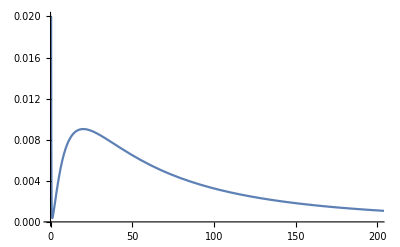

```mathematica
Plot[LogNormMixExp[t, w1, μ1, σ1, λ]/.yoAllProbmixEFB⟦2⟧,{t,0,300},PlotRange->{{0,200},{0,0.02}}]
```

```mathematica
consFB={yoAllProbmixEFB⟦2,1⟧,yoAllProbmixEFB⟦2,-1⟧}
```

{w1→0.0384615,λ→7.91949}

```mathematica
yoAllProbmix2EFB=ParallelTable[NMaximize[{Total[(Table[((((Log[LogNorm2MixExp[#[[5]]/1000,w1,w2,μ1,σ1,μ2,σ2,λ]])*(#[[1]])))&/@polySppGridRescal[[i]]),{i,1,Length[polySppGridRescal]}])//Flatten]+Total[(Table[((((Log[LogNorm2MixExp[#[[5]]/1000,w1,w2,μ1,σ1,μ2,σ2,λ]])*(#[[1]])))&/@polySppGridRescal[[i]]),{i,1,Length[polySppGridRescal]}])//Flatten]+(Total[(Table[((((Log[LogNorm2MixExp[#[[6]]/1000,w1,w2,μ1,σ1,μ2,σ2,λ]])*(#[[1]]))+(Log[LogNorm2MixExp[(#[[5]]/1000),w1,w2,μ1,σ1,μ2,σ2,λ]])*(#[[1]]))&/@noadmSppGridRescal[[i]]),{i,1,Length[noadmSppGridRescal]}])//Flatten]+Total[(Table[(((Log[LogNorm2MixExp[#[[6]]/1000,w1,w2,μ1,σ1,μ2,σ2,λ]])*(#[[1]]))+((#[[8]])*(Log[LogNorm2MixExp[(#[[5]]+1)/1000,w1,w2,μ1,σ1,μ2,σ2,λ]])*(#[[1]]))+((1-#[[8]])*(Log[LogNorm2MixExp[#[[7]]/1000,w1,w2,μ1,σ1,μ2,σ2,λ]])*(#[[1]])))&/@admSppGridRescal[[i]],{i,1,Length[admSppGridRescal]}]//Flatten)])/.consFB,1/26<w2<0.95,0<μ2<20,0<μ1<20,0.02<σ2,0.02<σ1},{w2,μ1,σ1,μ2,σ2},{MaxIterations->200,RandomSeed->i,Method->"DifferentialEvolution"}],{i,1,12}]
```

{{-148.471,{w2→0.411462,μ1→4.31178,σ1→0.663542,μ2→4.17049,σ2→1.57562}},{-147.594,{w2→0.937076,μ1→7.0669,σ1→0.02,μ2→4.19173,σ2→1.04055}},{-147.447,{w2→0.891395,μ1→4.93721,σ1→0.0547199,μ2→4.20449,σ2→1.19214}},{-148.471,{w2→0.550076,μ1→4.17049,σ1→1.57562,μ2→4.31178,σ2→0.663542}},{-148.471,{w2→0.411462,μ1→4.31178,σ1→0.663542,μ2→4.17049,σ2→1.57562}},{-148.471,{w2→0.550076,μ1→4.17049,σ1→1.57562,μ2→4.31178,σ2→0.663542}},{-148.471,{w2→0.550076,μ1→4.17049,σ1→1.57562,μ2→4.31178,σ2→0.663542}},{-147.073,{w2→0.1303,μ1→4.15364,σ1→1.1788,μ2→4.94756,σ2→0.0551489}},{-147.751,{w2→0.132394,μ1→4.33722,σ1→1.17033,μ2→4.9088,σ2→0.0770307}},{-148.471,{w2→0.550076,μ1→4.17049,σ1→1.57562,μ2→4.31178,σ2→0.663542}},{-147.17,{w2→0.920759,μ1→2.1153,σ1→0.02,μ2→4.36098,σ2→1.04812}},{-148.471,{w2→0.550076,μ1→4.17049,σ1→1.57562,μ2→4.31178,σ2→0.663542}}}

```mathematica
exp2={-147.072922066496,{w2->0.13029959536447247,μ1->4.153642961291457,σ1->1.1787983061494685,μ2->4.947562858164831,σ2->0.05514894551093972}}
```

{-147.073,{w2→0.1303,μ1→4.15364,σ1→1.1788,μ2→4.94756,σ2→0.0551489}}

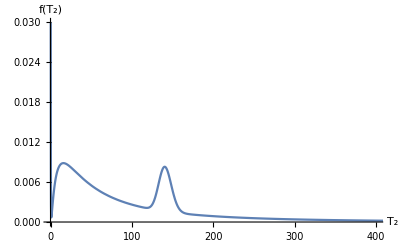

```mathematica
Plot[{LogNorm2MixExp[x,w1,w2,μ1,σ1,μ2,σ2,λ]/.consFB/.yoAllProbmix2EFB⟦8,2⟧}//Evaluate,{x,0,500}, AxesLabel->{"T_2","f(T_2)"},PlotRange->{{0,400},{0,0.03}}]
```

```mathematica
1-0.038461538461538464-0.13029959536447247
```

0.831239

```mathematica
cons3fb=Join[consFB,{w2->0.13029959536447247,μ2->4.947562858164831,σ2->0.05514894551093972}]
```

{w1→0.0384615,λ→7.91949,w2→0.1303,μ2→4.94756,σ2→0.0551489}

```mathematica
yoAllProbmix3EFB=ParallelTable[NMaximize[{Total[(Table[(((Log[LogNorm3MixExp[#[[5]]/1000,w1,w2,w3,μ1,σ1,μ2,σ2,μ3,σ3,λ]])*(#[[1]]))&/@polySppGridRescal[[i]]),{i,1,Length[polySppGridRescal]}])//Flatten]+Total[(Table[(((Log[LogNorm3MixExp[#[[5]]/1000,w1,w2,w3,μ1,σ1,μ2,σ2,μ3,σ3,λ]])*(#[[1]]))&/@polySppGridRescal[[i]]),{i,1,Length[polySppGridRescal]}])//Flatten]+(Total[(Table[((((Log[LogNorm3MixExp[#[[6]]/1000,w1,w2,w3,μ1,σ1,μ2,σ2,μ3,σ3,λ]])*(#[[1]]))+(Log[LogNorm3MixExp[(#[[5]]/1000),w1,w2,w3,μ1,σ1,μ2,σ2,μ3,σ3,λ]])*(#[[1]]))&/@noadmSppGridRescal[[i]]),{i,1,Length[noadmSppGridRescal]}])//Flatten]+Total[(Table[(((Log[LogNorm3MixExp[#[[6]]/1000,w1,w2,w3,μ1,σ1,μ2,σ2,μ3,σ3,λ]])*(#[[1]]))+((#[[8]])*(Log[LogNorm3MixExp[(#[[5]]+1)/1000,w1,w2,w3,μ1,σ1,μ2,σ2,μ3,σ3,λ]])*(#[[1]]))+((1-#[[8]])*(Log[LogNorm3MixExp[#[[7]]/1000,w1,w2,w3,μ1,σ1,μ2,σ2,μ3,σ3,λ]])*(#[[1]])))&/@admSppGridRescal[[i]],{i,1,Length[admSppGridRescal]}]//Flatten)])/.cons3fb,0<w3<0.83,0<μ3<10,0<μ1<10,0.01<σ3,0.05<σ1},{w3,μ1,σ1,μ3,σ3},{MaxIterations->200,RandomSeed->i,Method->"DifferentialEvolution"}],{i,1,12}]
```

{{-145.907,{w3→0.386664,μ1→4.23097,σ1→1.56148,μ3→4.01885,σ3→0.5271}},{-145.907,{w3→0.386664,μ1→4.23097,σ1→1.56148,μ3→4.01885,σ3→0.5271}},{-145.907,{w3→0.386664,μ1→4.23097,σ1→1.56148,μ3→4.01885,σ3→0.5271}},{-144.259,{w3→0.669836,μ1→3.65049,σ1→0.0768416,μ3→4.26242,σ3→1.29285}},{-144.259,{w3→0.669837,μ1→3.65049,σ1→0.0768416,μ3→4.26242,σ3→1.29285}},{-144.259,{w3→0.669836,μ1→3.65049,σ1→0.0768416,μ3→4.26242,σ3→1.29285}},{-144.259,{w3→0.669837,μ1→3.65049,σ1→0.0768416,μ3→4.26242,σ3→1.29285}},{-145.907,{w3→0.386664,μ1→4.23097,σ1→1.56148,μ3→4.01885,σ3→0.5271}},{-145.907,{w3→0.444575,μ1→4.01885,σ1→0.5271,μ3→4.23097,σ3→1.56148}},{-144.259,{w3→0.161402,μ1→4.26242,σ1→1.29285,μ3→3.65049,σ3→0.0768416}},{-144.259,{w3→0.161402,μ1→4.26242,σ1→1.29285,μ3→3.65049,σ3→0.0768416}},{-144.259,{w3→0.161402,μ1→4.26242,σ1→1.29285,μ3→3.65049,σ3→0.0768416}}}

```mathematica
exp3=yoAllProbmix3EFB[[10]]
```

{-144.259,{w3→0.161402,μ1→4.26242,σ1→1.29285,μ3→3.65049,σ3→0.0768416}}

```mathematica
exp3x={-144.25898245263602,{w3->0.16140235631515573,μ1->4.2624216841106675,σ1->1.2928533445812778,μ3->3.650493724495546,σ3->0.0768416258350312}}
```

{-144.259,{w3→0.161402,μ1→4.26242,σ1→1.29285,μ3→3.65049,σ3→0.0768416}}

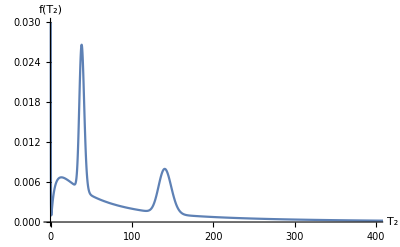

```mathematica
Plot[{LogNorm3MixExp[x,w1,w2,w3,μ1,σ1,μ2,σ2,μ3,σ3,λ]/.cons3fb/.yoAllProbmix3EFB⟦10,2⟧}//Evaluate,{x,0,500}, AxesLabel->{"T_2","f(T_2)"},PlotRange->{{0,400},{0,0.03}}]
```

```mathematica
cons4FBx=Join[cons3fb,{w3->0.16140235631515573,μ3->3.650493724495546,σ3->0.0768416258350312}]
```

{w1→0.0384615,λ→7.91949,w2→0.1303,μ2→4.94756,σ2→0.0551489,w3→0.161402,μ3→3.65049,σ3→0.0768416}

```mathematica
yoAllProbmix4EFB=ParallelTable[NMaximize[{(Total[(Table[(((Log[LogNorm4MixExp[#[[5]]/1000,w1,w2,w3,w4,μ1,σ1,μ2,σ2,μ3,σ3,μ4,σ4,λ]])*(#[[1]]))&/@polySppGridRescal[[i]]),{i,1,Length[polySppGridRescal]}])//Flatten]+Total[(Table[(((Log[LogNorm4MixExp[#[[5]]/1000,w1,w2,w3,w4,μ1,σ1,μ2,σ2,μ3,σ3,μ4,σ4,λ]])*(#[[1]]))&/@polySppGridRescal[[i]]),{i,1,Length[polySppGridRescal]}])//Flatten]+Total[(Table[((((Log[LogNorm4MixExp[#[[6]]/1000,w1,w2,w3,w4,μ1,σ1,μ2,σ2,μ3,σ3,μ4,σ4,λ]])*(#[[1]]))+(Log[LogNorm4MixExp[(#[[5]]/1000),w1,w2,w3,w4,μ1,σ1,μ2,σ2,μ3,σ3,μ4,σ4,λ]])*(#[[1]]))&/@noadmSppGridRescal[[i]]),{i,1,Length[noadmSppGridRescal]}])//Flatten]+Total[(Table[(((Log[LogNorm4MixExp[#[[6]]/1000,w1,w2,w3,w4,μ1,σ1,μ2,σ2,μ3,σ3,μ4,σ4,λ]])*(#[[1]]))+((#[[8]])*(Log[LogNorm4MixExp[(#[[5]]+1)/1000,w1,w2,w3,w4,μ1,σ1,μ2,σ2,μ3,σ3,μ4,σ4,λ]])*(#[[1]]))+((1-#[[8]])*(Log[LogNorm4MixExp[#[[7]]/1000,w1,w2,w3,w4,μ1,σ1,μ2,σ2,μ3,σ3,μ4,σ4,λ]])*(#[[1]])))&/@admSppGridRescal[[i]],{i,1,Length[admSppGridRescal]}]//Flatten)])/.cons4FBx,1/26<w4<0.67,0<μ4<10,0<μ1<10,0.01<σ4,0.05<σ1},{w4,μ1,σ1,μ4,σ4},{MaxIterations->200,RandomSeed->i,Method->"DifferentialEvolution"}],{i,13,24}]
```

{{-142.925,{w4→0.540522,μ1→4.37609,μ4→4.30003,σ1→0.16399,σ4→1.6507}},{-143.579,{w4→0.208879,μ1→3.92105,μ4→4.49679,σ1→1.30407,σ4→0.162331}},{-143.61,{w4→0.165738,μ1→4.30653,μ4→4.27169,σ1→1.49953,σ4→0.502917}},{-143.458,{w4→0.24205,μ1→3.68419,μ4→4.42502,σ1→1.7313,σ4→0.318296}},{-143.988,{w4→0.237767,μ1→4.03136,μ4→4.47732,σ1→1.80819,σ4→0.725424}},{-143.962,{w4→0.0833639,μ1→4.58022,μ4→4.37801,σ1→1.78585,σ4→0.036474}},{-142.984,{w4→0.464024,μ1→4.50586,μ4→4.12549,σ1→0.171223,σ4→1.44435}},{-143.793,{w4→0.365771,μ1→4.55909,μ4→3.93152,σ1→0.636296,σ4→1.53642}},{-143.44,{w4→0.154992,μ1→4.10823,μ4→4.39175,σ1→1.41938,σ4→0.437256}},{-143.628,{w4→0.281456,μ1→4.2816,μ4→4.41622,σ1→1.61885,σ4→0.608301}},{-143.136,{w4→0.273149,μ1→4.39137,μ4→4.51463,σ1→1.70637,σ4→0.257333}},{-144.297,{w4→0.286347,μ1→3.54595,μ4→4.59945,σ1→1.96,σ4→0.646766}}}

```mathematica
exp4x=yoAllProbmix4EFB[[1]]
```

{-142.925,{w4→0.540522,μ1→4.37609,μ4→4.30003,σ1→0.16399,σ4→1.6507}}

```mathematica
exp4={-143.22646192095488,{w4->0.04413377898291195,μ1->3.646126898002253,σ1->0.0720640229856372,μ4->4.369665248267683,σ4->0.029970126512555463}}
```

{-143.226,{w4→0.0441338,μ1→3.64613,σ1→0.072064,μ4→4.36967,σ4→0.0299701}}

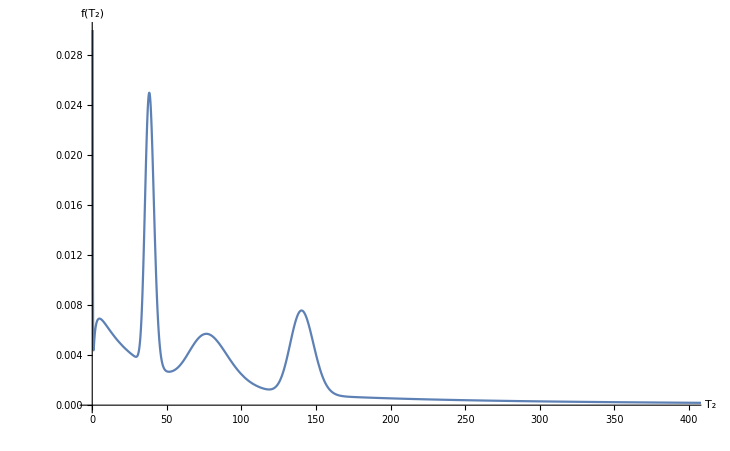

```mathematica
Plot[{LogNorm4MixExp[x,w1,w2,w3,w4,μ1,σ1,μ2,σ2,μ3,σ3,μ4,σ4,λ]/.cons4FBx/.yoAllProbmix4EFB[[1,2]]}//Evaluate,{x,0,500}, AxesLabel->{"T_2","f(T_2)"},PlotRange->{{0,400},{0,0.03}}]
```

#### Best-supported model and parameter estimates

```mathematica
lnLiffs=2*{exp1[[1]]-expX[[1]],exp2[[1]]-exp1[[1]],exp3[[1]]-exp2[[1]],exp4[[1]]-exp3[[1]]}
```

{6.04394,5.0722,5.62788,2.06504}

```mathematica
SetPrecision[1 - CDF[ChiSquareDistribution[3], #], 3] & /@ lnLiffs
```

{0.109,0.167,0.131,0.559}

```mathematica
lnLiffs4={2*(exp4[[1]]-expX[[1]])}
```

{18.8091}

```mathematica
lnLiffs4={2*(exp4x[[1]]-expX[[1]])}
```

{19.4121}

```mathematica
lnLiffs3={2*(exp3⟦1⟧-expX⟦1⟧)}
```

{16.744}

```mathematica
lnLiffs2={2*(exp2[[1]]-expX⟦1⟧)}
```

{11.1161}

```mathematica
lnLiffs1={2*(exp1[[1]]-expX[[1]])}
```

{6.4767}

```mathematica
SetPrecision[1-CDF[ChiSquareDistribution[3],#],3]&/@lnLiffs1
```

{0.0906}

```mathematica
SetPrecision[1-CDF[ChiSquareDistribution[6],#],3]&/@lnLiffs2
```

{0.0849}

```mathematica
SetPrecision[1-CDF[ChiSquareDistribution[9],#],3]&/@lnLiffs3
```

{0.0529}

```mathematica
SetPrecision[1-CDF[ChiSquareDistribution[12],#],3]&/@lnLiffs4
```

{0.0791}

Log normal modes and weights for each model

```mathematica
exp1
```

{-149.393,{w1→0.0384615,μ1→4.26328,σ1→1.12551,λ→7.91949}}

```mathematica
a=4.263278994560994;b=1.1255094060263733;ⅇ^(a-b^2)
```

20.0155

```mathematica
1-0.0384
```

0.9616

```mathematica
exp2
```

{-147.073,{w2→0.1303,μ1→4.15364,σ1→1.1788,μ2→4.94756,σ2→0.0551489}}

```mathematica
consFB
```

{w1→0.0384615,λ→7.91949}

```mathematica
1-0.038461538461538464-0.13029959536447247
```

0.831239

```mathematica
a=4.153642961291457;b=1.1787983061494685;ⅇ^(a-b^2)
```

15.8644

```mathematica
a=4.947562858164831;b=0.05514894551093972;ⅇ^(a-b^2)
```

140.404

Best - fitting model (single exponential + 3 log normals)

```mathematica
cons3fb
```

{w1→0.0384615,λ→7.91949,w2→0.1303,μ2→4.94756,σ2→0.0551489}

```mathematica
exp3x
```

{-144.259,{w3→0.161402,μ1→4.26242,σ1→1.29285,μ3→3.65049,σ3→0.0768416}}

```mathematica
a=4.262421691990371;b=1.2928533560799038;ⅇ^(a-b^2)
```

13.3425

```mathematica
a=3.650493731878684;b=0.07684163690415582;ⅇ^(a-b^2)
```

38.267

```mathematica
ww1=0.038461538461538464;ww2=0.13029959536447247;ww3=0.6698364973130387;ww4=1-ww1-ww2-ww3
```

0.161402

```mathematica
Params={μ1->3.650493731878684,σ1->0.07684163690415582,μμ2->4.947562858164831,σ2->0.05514894551093972,μ3->4.262421691990371,σ3->1.2928533560799038}
```

{μ1→3.65049,σ1→0.0768416,μμ2→4.94756,σ2→0.0551489,μ3→4.26242,σ3→1.29285}

```mathematica
Params2=#[[2]]&/@Params
```

{3.65049,0.0768416,4.94756,0.0551489,4.26242,1.29285}

```mathematica
1-0.038461538461538464-0.1303-0.16140235631515573-0.5405222842080317
```

0.129314

```mathematica
exp4x
```

{-142.925,{w4→0.540522,μ1→4.37609,μ4→4.30003,σ1→0.16399,σ4→1.6507}}

```mathematica
cons4FBx
```

{w1→0.0384615,λ→7.91949,w2→0.1303,μ2→4.94756,σ2→0.0551489,w3→0.161402,μ3→3.65049,σ3→0.0768416}

```mathematica
a=4.3760910076894;b=0.16398951197935752;ⅇ^(a-b^2)
```

77.4164

```mathematica
a=4.947562858164831;b=0.05514894551093972;ⅇ^(a-b^2)
```

140.404

```mathematica
a=3.646126898002253;b=0.0720640229856372;ⅇ^(a-b^2)
```

38.1274

```mathematica
a=4.300028089680241;b=1.6507029458702016;ⅇ^(a-b^2)
```

4.83175

### Functions for grid processing

For each point along one axis of the grid, we retain the highest likelihood position (i.e. last position : [[-1]]) (i.e. the MLE for the other axes).

```mathematica
gridMLE::usage="gridMLE[gr_,l_,pos_] extracts the discreticed marginal lnL for a parameter specified by its position (pos). The dimensionality of the lnL grid is specified by l";
```

```mathematica
gridMLE[gr_,l_,pos_]:=SortBy[{#⟦pos⟧,#⟦1⟧}&/@((SortBy[#,#⟦1⟧&]⟦-1⟧)&/@SplitBy[SortBy[Flatten[gr,l],#⟦pos⟧&],#⟦pos⟧&]),#⟦1⟧&]
```

This is an amended function so invalid points in the grid are removed from the splitting, sorting (and eventually rescaling) process.

```mathematica
gridMLE2[gr_,l_,pos_,posA_,posB_]:=SortBy[{#⟦pos⟧,#⟦1⟧}&/@((SortBy[#,#⟦1⟧&]⟦-1⟧)&/@SplitBy[SortBy[(Select[Flatten[gr,l],#⟦posA⟧<=#⟦posB⟧&]),#⟦pos⟧&],#⟦pos⟧&]),#⟦1⟧&]
```

```mathematica
approxFact::usage="approxFact[l_] estimates an approximate rescaling factor for the composite lnL values in a list. We assume that the first and last entry correspond to the lower and upper 95% bound of the paramter and uses the midpoint of these two extremes (hence the factor of 1/2) to work out a rescaling factor. After rescaling, the MLE in the grid is 2 lnL from this midpoint.";
```

```mathematica
approxFact[l_] :=(Max[l]-(l⟦1⟧+l⟦-1⟧)/2)/2;
```

```mathematica
rescalGrid::usage="rescalGrid[gr_,l_,fact_] replaces the lnCL values in a discretized grid with approximate probabilities. These are obtained by i) rescaling lnCL by a specified factor (fact) and ii) normalising the resulting approximate likelihoods by the total in the grid";
```

```mathematica
rescalGrid[gr_,l_,fact_]:=Module[{flatgrid=Flatten[gr,l],probs,tprobs},
probs=Exp[#⟦1⟧/fact]&/@flatgrid;
tprobs =Total[probs];
Table[ReplacePart[flatgrid⟦i⟧, 1 ->probs⟦i⟧/tprobs],{i,1,Length[flatgrid]}]];
```

```mathematica
rescalGrid2[gr_,l_,fact_,posA_,posB_]:=Module[{flatgrid=Select[Flatten[gr,l],#⟦posA⟧<=#⟦posB⟧&],probs,tprobs},
probs=Exp[#⟦1⟧/fact]&/@flatgrid;
tprobs =Total[probs];
Table[ReplacePart[flatgrid⟦i⟧, 1 ->probs⟦i⟧/tprobs],{i,1,Length[flatgrid]}]];
```

### Functions for mixture fitting

```mathematica
LogNorm[t_,μ_,σ_]:=(ⅇ^(-(Log[t]-μ)^2/(2 σ^2)))/(√(2 π (t σ)^2));
```

```mathematica
LogNormMix2[t_,w_,μ1_,μ2_,σ1_,σ2_]:=(w LogNorm[t,μ1,σ1])+((1-w)LogNorm[t,μ2,σ2]);
```

```mathematica
LogNormMix3[t_,w1_,w2_,μ1_,σ1_,μ2_,σ2_,μ3_,σ3_]:=(w1 LogNorm[t,μ1,σ1])+(w2 LogNorm[t,μ2,σ2])+((1-w1-w2) LogNorm[t,μ3,σ3]);
```

```mathematica
LogNormMix4[t_,w1_,w2_,w3_,μ1_,σ1_,μ2_,σ2_,μ3_,σ3_,μ4_,σ4_]:=(w1 LogNorm[t,μ1,σ1])+(w2 LogNorm[t,μ2,σ2])+(w3 LogNorm[t,μ3,σ3])+((1-w1-w2-w3) LogNorm[t,μ4,σ4]);
```

```mathematica
LogNorm2MixExp[t_,w1_,w2_,μ1_,σ1_,μ2_,σ2_,λ_]:=w1 λ ⅇ^(-λ t)+(w2 LogNorm[t,μ2,σ2])+((1-w1-w2) LogNorm[t,μ1,σ1]);
```

```mathematica
LogNorm3MixExp[t_,w1_,w2_,w3_,μ1_,σ1_,μ2_,σ2_,μ3_,σ3_,λ_]:=w1 λ ⅇ^(-λ t)+(w2 LogNorm[t,μ2,σ2])+(w3 LogNorm[t,μ3,σ3])+((1-w1-w2-w3) LogNorm[t,μ1,σ1]);
```

```mathematica
LogNorm4MixExp[t_,w1_,w2_,w3_,w4_,μ1_,σ1_,μ2_,σ2_,μ3_,σ3_,μ4_,σ4_,λ_]:=w1 λ ⅇ^(-λ t)+(w2 LogNorm[t,μ2,σ2])+(w3 LogNorm[t,μ3,σ3])+(w4 LogNorm[t,μ4,σ4])+((1-w1-w2-w3-w4) LogNorm[t,μ1,σ1]);
```

```mathematica
LogNormMixExp[t_,w_,μ1_,σ1_,v_]:=w λ ⅇ^(-λ t)+((1-w)LogNorm[t,μ1,σ1]);
```

```mathematica
ExpFun[time_,λ_]:=λ ⅇ^(-λ time)
```